```mathematica
Clear["Global`*"]
Needs["Developer`"]
```

## Dumping and Reading .msh File - Modular

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[sprtr,ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
If[$OperatingSystem=="MacOSX",sprtr="_";,0.0];
If[$OperatingSystem=="Windows",sprtr="_";,0.0];
If[$OperatingSystem=="Linux",sprtr="_";,0.0];

ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"mesh"}]
```

/Users/qzmfrank/Codes/rte2dvis/notebook/mesh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

OpenRead::noopen: Cannot open "/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial.msh".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 2}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 3}].

ConstantArray::argt: ConstantArray called with 0 arguments; 2 or 3 arguments are expected.

{False,False}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

OpenRead::noopen: Cannot open "/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26.msh".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 2}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 3}].

ConstantArray::argt: ConstantArray called with 0 arguments; 2 or 3 arguments are expected.

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial_dat/triangles.dat

Import::nffil: File not found during Import.

{False,False}

{Norm[$Failed]+Norm[-ConstantArray[0.,{Read[$Failed,Number],2}]],Norm[$Failed]+Norm[-Floor[ConstantArray[]]]}

## Direct Integral Solver - Sequential, Interpretive and Partially Compiled

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,Phasef,Phasef1,Phasef2,PhaseFunc,PhaseFunc1,phis,Nd]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
mus[{x_,y_}]:=0.5Log[2.0]
mua[{x_,y_}]:=Log[2.0]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.6;
Phasef1[m_]:=g^Abs[m]
Phasef2[m_]:=If[m==0,1.0,0.0]
Phasef=Phasef1;
PhaseFunc1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi])),CompilationTarget:>"C"];
PhaseFunc=PhaseFunc1;
phis=0;
Nd=50;

ClearAll[iG,iL,Rank,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
Rank[x_]:=Length/@{x,xᵀ}//Quiet
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rXYPreCalc,r2rRPreCalc,r2rPhiPreCalc,r2rFPreCalc,SignedAreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
RcPreCalc[pt_]:=With[{a=Norm[#⟦1⟧-#⟦2⟧];b=Norm[#⟦1⟧-#⟦2⟧];c=Norm[#⟦1⟧-#⟦2⟧];},s=0.5(a+b+c);(a b c)/Sqrt[s(s-a)(s-b)(s-c)]]&/@pt
r2rXYPreCalc[cntr_]:=Outer[If[#1<#2,Subtract@@cntr⟦{#1,#2}⟧,{0.0,0.0}]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#-#ᵀ&
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
r2rPhiPreCalc[cntr_]:=Outer[If[#1≠#2,(Subtract@@cntr⟦{#1,#2}⟧//ArcTan[#⟦1⟧,#⟦2⟧]&),0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray
r2rFPreCalc[r2rPhi_,phis_]:=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];
SignedAreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Times[#,0.5]&;

ClearAll[Np,p,t,Nn,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc,Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea,TRc,musTbl,muaTbl,mutTbl]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nn=Ns;Nm=2Nd+1;Ng=Nn*Nm;
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nn,Nm,Ng}=",{Ns,Nd,Nn,Nm,Ng}];
gTbl=Phasef/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rXY=(r2rXY=r2rXYPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rPhi=(r2rPhi=r2rPhiPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rF=(r2rF=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];)//AbsoluteTiming//#⟦1⟧&;
TsignedArea=(signedArea=SignedAreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=Abs[signedArea];)//AbsoluteTiming//#⟦1⟧&;
TRc=(Rc=Module[{a,b,c,s},
a=Norm[#⟦1⟧-#⟦2⟧];
b=Norm[#⟦2⟧-#⟦3⟧];
c=Norm[#⟦3⟧-#⟦1⟧];
s=0.5(a+b+c);
(a b c)/Sqrt[s(s-a)(s-b)(s-c)]
]&/@pt//Times[#,0.25]&;)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}=",{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}//{Total[#],#}&];
Print["{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}=",PackedArrayQ/@{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}];
musTbl=mus/@cntr//ToPackedArray;
muaTbl=mua/@cntr//ToPackedArray;
mutTbl=musTbl+muaTbl;
Print["{musTbl,muaTbl,mutTbl}=",{musTbl,muaTbl,mutTbl}//Map[{PackedArrayQ[#],Rank[#]}&,#]&];


ClearAll[V,VRe,VIm,VElemtRe,VElemtIm,TVRe,TVIm]
VElemtRe=area⟦#⟦1⟧⟧Cos[#⟦2⟧phis]&;
VElemtIm=area⟦#⟦1⟧⟧Sin[#⟦2⟧phis]&;
VElemt=area⟦#⟦1⟧⟧Exp[-ⅈ#⟦2⟧phis]&;
TVRe=(VRe=1.0*VElemtRe[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
TVIm=(VIm=1.0*VElemtIm[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
V=1.0*VRe-1.0ⅈ*VIm;
Print["{TVRe,TVIm}=",{TVRe,TVIm}//{Total[#],#}&];
Print["{V,VRe,VIm}=",PackedArrayQ/@{V,VRe,VIm}];
Print["Norm[V]=",Norm[V]];

ClearAll[Zon1,Zon2,Zoff,vTblC,uTblC,TZon1,TZon2,TZoff,TvTblC,TuTblC]
TZon1=(Zon1=2π area+2 π^(1/2)mutTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZon2=(Zon2=-2 π^(1/2)musTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZoff=(Zoff=Outer[If[#2>#1,area⟦#1⟧area⟦#2⟧/r2rR⟦#1,#2⟧,0.0]&,Range[Ns],Range[Ns]]//ToPackedArray//#+#ᵀ&;)//AbsoluteTiming//#⟦1⟧&;

TvTblC=(vTblC=Compile[{{r2rPhi,_Real,2},{Ns,_Integer},{Nd,_Integer}},
Table[Exp[-ⅈ r2rPhi⟦n,np⟧Range[-Nd,Nd]],{n,Ns},{np,Ns}],
Parallelization->True
,CompilationTarget:>"C"
][r2rPhi,Ns,Nd];)//AbsoluteTiming//#⟦1⟧&;
TuTblC=(uTblC=Compile[{{musTbl,_Real,1},{mutTbl,_Real,1},{gTbl,_Real,1},{vTblC,_Complex,3},{r2rPhi,_Real,2},{Ns,_Integer}},
Table[mutTbl⟦np⟧vTblC⟦n,np⟧*-musTbl⟦np⟧gTbl vTblC⟦n,np⟧*,{n,Ns},{np,Ns}],
Parallelization->True
,CompilationTarget:>"C"
][musTbl,mutTbl,gTbl,vTblC,r2rPhi,Ns];
)//AbsoluteTiming//#⟦1⟧&;

Print["{TZon1,TZon2,TZoff,TvTblC,TuTblC}=",{TZon1,TZon2,TZoff,TvTblC,TuTblC}//{Total[#],#}&];
Print["{Zon1,Zon2,Zoff,vTblC,uTblC}=",PackedArrayQ/@{Zon1,Zon2,Zoff,vTblC,uTblC}];

ClearAll[ZDotXC0,ZDotXC,ZDotXCcounter]
ZDotXCcounter=0;
ZDotXC0=Compile[{{X,_Complex,1},{Ns,_Integer},{Nd,_Integer},{gTbl,_Real,1},{Zon1,_Real,1},{Zon2,_Real,1},{Zoff,_Real,2},{vTblC,_Complex,3},{uTblC,_Complex,3}},
  Module[{Xp,Yp,temp,n,np},
    Xp=Partition[X,2Nd+1];
    Flatten@Table[
      temp=ConstantArray[0.0+0.0I,2Nd+1];
      For[np=1,np<=Ns,np++,
        If[np==n,
          temp+=Zon1[[n]]Xp[[n]]+Zon2[[n]]gTbl Xp[[n]];,
          temp+=Zoff[[n,np]](Xp[[np]].uTblC[[n,np]])vTblC[[n,np]];
        ];  
      ];  
      temp
      ,{n,Ns}]
  ],  
  Parallelization->True
  ,CompilationTarget:>"C"
][#,Ns,Nd,gTbl,Zon1,Zon2,Zoff,vTblC,uTblC]&;
ZDotXC[V_]:=Module[{},ZDotXCcounter++;ZDotXC0[V]]
Print["ZDotXC[V] time=",ZDotXC[V]//AbsoluteTiming//#[[1]]&];


ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
,CompilationTarget:>"C"
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];

ClearAll[damp,Tdamp1,damp1]
Tdamp1=(damp1=Exp[-mutTbl⟦1⟧cntr⟦All,1⟧];)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp1=",Tdamp1];
Print["damp1=",damp1//PackedArrayQ];

ClearAll[OpticalPathC,damp2C,Tdamp2C]
OpticalPathC=Compile[{{P0,_Real,1},{phi,_Real},{mutTbl,_Real,1},{pt,_Real,3},{Ns,_Integer}},
Module[{np,tau=0.0},For[np=1,np≤Ns,np++,tau+=mutTbl⟦np⟧*HalfLineTriangleSegmentC[phi,P0,pt⟦np⟧];];tau]
(*,CompilationTarget:>"C"*)
][#1,#2,mutTbl,pt,Ns]&;
(*
Tdamp2C=(damp2C=Exp[Table[-OpticalPathC[cntr⟦n⟧,phis+π],{n,Ns}]]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp2C=",Tdamp2C]
Print["damp2C=",damp2C//PackedArrayQ];
Print["Norm[damp2C-damp1]=",Norm[damp2C-damp1]]

damp=damp2C;
ClearAll[Von,Voff,Vsc,TVsc]
TVsc=(
Von=musTbl √(area/π)damp;
Voff=((Zoff r2rF)ᵀ(damp musTbl))ᵀ;
Vsc=Von(Partition[V,Nm]ᵀg)ᵀ;
For[n=1,n≤Ns,n++,
For[np=1,np≤Ns,np++,
Vsc⟦n⟧+=Voff⟦n,np⟧vTblC⟦n,np⟧;
];
];
Vsc=Flatten[Vsc];)//AbsoluteTiming//#⟦1⟧&;
Print["Vsc=",PackedArrayQ[Vsc]];
Print["TVsc=",TVsc];
ClearAll[sol2sc,Tsol2sc,sol2scp]
Tsol2sc=(sol2sc=LinearSolve[ZDotXC[#]&,Vsc,Method->{"Krylov",Tolerance->Norm[Vsc]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2sc=",Tsol2sc];
Print["Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=",Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]];
Print["Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=",Max[Norm/@(ZDotXC[sol2sc]-Vsc)]/Norm[Vsc]];
sol2scp=Partition[sol2sc,Nm];
Print["sym sol2sc=",Table[Norm[sol2scp⟦n⟧-sol2scp⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];
Print["Nd residual=",(sol2scp⟦All,1⟧//Map[Norm,#]&//Norm)/(sol2scp⟦All,Nd+1⟧//Map[Norm,#]&//Norm)];

ClearAll[A,y,CoordTbl,nTbl,data,n,pltstr,fluence]
sol2scp=Partition[sol2sc,Nm];
y=0.5;A=Total[area];
CoordTbl=Table[{x,y},{x,0.01,0.99,0.9 √(A/N[Ns])}];
nTbl=PickTriangle/@CoordTbl;
data=Transpose@{CoordTbl⟦All,1⟧,sol2scp⟦nTbl,Nd+1⟧//Re};
For[n=1,n≤Length[data],n++,data⟦n,2⟧+=Exp[-OpticalPathC[CoordTbl⟦n⟧,phis+π]]/(2π);];
pltstr="NEW FLUENCE\n"<>"Nd="<>ToString[Nd]<>",Ns="<>ToString[Ns]<>",phis="<>ToString[phis]<>",μ_a="<>ToString[mua[{0,0}]]<>",μ_s="<>ToString[mus[{0,0}]]<>",g="<>ToString[g]<>",y="<>ToString[y];
Print@Show[
ListPlot[data,PlotRange->{0,1/(2π)+0.04},PlotLabel->pltstr,AxesLabel->{"x","fluence"},PlotStyle->{PointSize[Medium]},ImageSize->Medium],
Plot[Exp[-mut[{0.,0.}]x]/(2π),{x,0,1},PlotStyle->{Red,Dashed,Thick}]
]
fluence=Interpolation[{cntr,sol2scp⟦All,Nd+1⟧32}//Chop//Transpose]//Quiet;
DensityPlot[fluence[x,y]+Exp[-mutTbl⟦1⟧x]/(2π),{x,0,1},{y,0,1},AspectRatio->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->Medium,AxesLabel->{"x","y"}]//Quiet;
*)
```

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/triangles.dat

CCompilerDriver`CreateLibrary::cmperr: Compile error: "/usr/local/lib/gcc/x86_64-apple-darwin12.4.0/4.8.1/include-fixed/math.h:53:23: fatal error: sys/cdefs.h: No such file or directory"

Compile::nogen: A library could not be generated from the compiled function.

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nn,Nm,Ng}={162,50,162,101,16362}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}={0.3757,{0.00017,0.00015,0.06592,0.07751,0.14002,0.09067,0.00048,0.00005,0.00071}}

{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}={True,True,True,True,True,True,True,True,True}

{musTbl,muaTbl,mutTbl}={{True,{162,1}},{True,{162,1}},{True,{162,1}}}

{TVRe,TVIm}={0.1194,{0.06094,0.05847}}

{V,VRe,VIm}={True,True,True}

Norm[V]=0.80037

CCompilerDriver`CreateLibrary::cmperr: Compile error: "/usr/local/lib/gcc/x86_64-apple-darwin12.4.0/4.8.1/include-fixed/math.h:53:23: fatal error: sys/cdefs.h: No such file or directory"

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::cmperr: Compile error: "/usr/local/lib/gcc/x86_64-apple-darwin12.4.0/4.8.1/include-fixed/math.h:53:23: fatal error: sys/cdefs.h: No such file or directory"

Compile::nogen: A library could not be generated from the compiled function.

{TZon1,TZon2,TZoff,TvTblC,TuTblC}={0.63868,{0.00006,0.00002,0.06183,0.33415,0.24262}}

{Zon1,Zon2,Zoff,vTblC,uTblC}={True,True,True,True,True}

CCompilerDriver`CreateLibrary::cmperr: Compile error: "/usr/local/lib/gcc/x86_64-apple-darwin12.4.0/4.8.1/include-fixed/math.h:53:23: fatal error: sys/cdefs.h: No such file or directory"

Compile::nogen: A library could not be generated from the compiled function.

ZDotXC[V] time=0.23696

CCompilerDriver`CreateLibrary::cmperr: Compile error: "/usr/local/lib/gcc/x86_64-apple-darwin12.4.0/4.8.1/include-fixed/math.h:53:23: fatal error: sys/cdefs.h: No such file or directory"

Compile::nogen: A library could not be generated from the compiled function.

Tdamp1=0.00004

damp1=True

```mathematica
ClearAll[QUADRULES,VscNEW]
QUADRULES={DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[8,0,1],LegendreRule[3,0,1]}};
Print["time=",(VscNEW=ParallelTable[NField[cntr⟦n⟧,m,QUADRULES]*area⟦n⟧,{n,Nn},{m,-Nd,Nd}]//Flatten[#,1]&;)//AbsoluteTiming//#⟦1⟧&];
ClearAll[sol2scNEW,Tsol2scNEW,sol2scNEWp]
Tsol2scNEW=(sol2scNEW=LinearSolve[ZDotXC[#]&,VscNEW,Method->{"Krylov",Tolerance->Norm[VscNEW]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2scNEW=",Tsol2scNEW];
Print["Norm[ZDotXC0[sol2scNEW]-VscNEW]/Norm[VscNEW]=",Norm[ZDotXC0[sol2scNEW]-VscNEW]/Norm[VscNEW]];
ClearAll[sol2scNEWp]
sol2scNEWp=Partition[sol2scNEW,Nm]⟦All,Nd+1;;Nm⟧;
Norm/@sol2scNEWp⟦10⟧//ListPlot[#,PlotRange->All]&
```

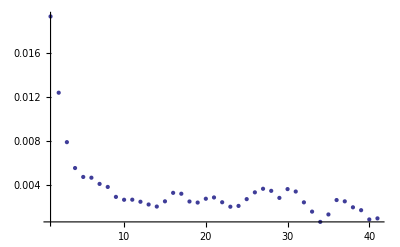

```mathematica
Norm/@sol2scNEWp⟦1⟧//ListPlot[#,PlotRange->All]&
```

## Quadrature Rules and Numerical Integration - Modular

The following cell shall only be run once!!!

```mathematica
$LibraryPath
```

{/Applications/Mathematica.app/SystemFiles/Autoload/PacletManager/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Kernel/SystemResources/LibraryResources/MacOSX-x86-64,/Users/qzmfrank/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64,/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/AddOns/Applications/DocumentationSearch/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/CalendarTools/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/CUDALink/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/FDLLink/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/HTTPClient/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/LibraryLink/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/OpenCLLink/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/OpenSURF/LibraryResources/MacOSX-x86-64,/Applications/Mathematica.app/SystemFiles/Links/TetGenLink/LibraryResources/MacOSX-x86-64,/Users/qzmfrank/Codes/rte2dvis/notebook/../MLL-lib}

```mathematica
Needs["CCompilerDriver`"]
$LibraryPath=AppendTo[$LibraryPath,FileNameJoin[{NotebookDirectory[],"../MLL-lib"}]];
ClearAll[LegendreRuleMLL,DunavantRuleMLL]
LegendreRuleMLL=LibraryFunctionLoad["lib-franklin","LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRuleMLL=LibraryFunctionLoad["lib-franklin","DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
(*
SetDirectory[FileNameJoin[{NotebookDirectory[],"../ML-exe"}]];
Install["DunavantRule.exe"];
Install["LegendreRule.exe"];
(*Install More Executables Here...*)
ResetDirectory[];
*)
```

```mathematica
ClearAll[LegendreRule,DunavantRule]
LegendreRule[order_,xmin_,xmax_]:=LegendreRuleMLL[order,xmin,xmax]//Quiet;
DunavantRule[rule_,p_]:=Module[{qx,qy,q,w},
{qx,qy,w}=DunavantRuleMLL[rule,p]//Quiet;
q={qx,qy}ᵀ//ToPackedArray;
w=w//ToPackedArray;
{q,w}
]
ClearAll[QuadratureProduct2D]
QuadratureProduct2D[{q1_, w1_}, {q2_, w2_}] := Module[{q,w},
q=Outer[{#1,#2}&,q1,q2]//Flatten[#,1]&//N//ToPackedArray;
w=Outer[Times,w1,w2]//Flatten[#,1]&//N//ToPackedArray;
{q,w}
]
ClearAll[NIntegrateTriangleDuffyMethod,NIntegrateTriangleDunavantMethod]
NIntegrateTriangleDuffyMethod[p_,fun_,{q_,w_}]:=
Module[{qq,ww,P0P1,P1P2,P1P2Sq,λ1,λ2,A,b,n,DetA},
P0P1=p⟦2⟧-p⟦1⟧;
P1P2=p⟦3⟧-p⟦2⟧;
A={P0P1,P1P2}//Transpose;
DetA=Abs[Det[A]];
b=p⟦1⟧;
n=Length[q];
P1P2Sq=Total[P1P2^2];
λ1=P0P1.P1P2/P1P2Sq;
λ2=DetA/P1P2Sq;
qq=A.{#⟦1⟧,#⟦1⟧#⟦2⟧}+b&/@q;
ww=Table[w⟦i⟧/Sqrt[(q⟦i,2⟧+λ1)^2+λ2^2],{i,n}];
DetA/Sqrt[P1P2Sq]*∑_(i=1)^n ww⟦i⟧fun[qq⟦i⟧]
]
NIntegrateTriangleDunavantMethod[p_,fun_,{q_,w_}]:=
(*weights are normalized to 1.0
abssicas are for (0,0) (1,0) (0,1)*)
Module[{n,A,qq},
n=Length[q];
A={p⟦2⟧-p⟦1⟧,p⟦3⟧-p⟦1⟧}ᵀ;
qq=A.#+p⟦1⟧&/@q;
0.5*Abs[Det[A]]∑_(i=1)^n w⟦i⟧fun[qq⟦i⟧]
]

ClearAll[NIntegrateTriangleArcSinhMethod]
NIntegrateTriangleArcSinhMethod[P_,fun_,{{ξu_,wu_},{ξv_,wv_}}]:=
Module[{P0P1,P0P2,P1P2,LP1P2,uP1P2,h,Ah,x1p,x2p,uL,uU,vL,vU,xyij,Wij,Nij},
P0P1=P⟦2⟧-P⟦1⟧;
P0P2=P⟦3⟧-P⟦1⟧;
P1P2=P⟦3⟧-P⟦2⟧;
LP1P2=Norm[P1P2];
uP1P2=P1P2/LP1P2;
h=(-P1P2⟦1⟧P⟦1,2⟧+P0P2⟦1⟧P⟦2,2⟧-P0P1⟦1⟧P⟦3,2⟧)/LP1P2;
x1p=P0P1.uP1P2//N;
x2p=P0P2.uP1P2//N;
uL=ArcSinh[x1p/h];
uU=ArcSinh[x2p/h];
vL=0;
vU=h;
Ah=h({{uP1P2⟦1⟧, -uP1P2⟦2⟧}, {uP1P2⟦2⟧, uP1P2⟦1⟧}});
xyij=Outer[{#2Sinh[uL+(uU-uL)#1],#2}&,ξu,ξv]//Flatten[#,1]&//Map[P⟦1⟧+Ah.#&,#]&;
Wij=Outer[Times,wu,wv]//Flatten[#,1]&;
Nij=Length[wu]Length[wv];
Abs[h(uU-uL)]∑_(k=1)^Nij Wij⟦k⟧fun[xyij⟦k⟧]
]
ClearAll[VscnmFunc,VscnmFuncR]
VscnmFunc[m_,r_,rp_]:=Module[{dr,R,Phi},
dr=r-rp;R=Norm[dr];Phi=ArcTan[dr⟦1⟧,dr⟦2⟧];
(*Exp[-ⅈ m Phi]/R*mus[rp]*PhaseFunc[Phi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m Phi]/R*mus[rp]*PhaseFunc[Phi-phis]*Exp[-rp⟦1⟧]
]
VscnmFuncR[m_,r_,rp_]:=With[{Phi=(r-rp)//ArcTan[#⟦1⟧,#⟦2⟧]&},
(*Exp[-ⅈ m Phi]*mus[rp]*PhaseFunc[Phi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m Phi]*mus[rp]*PhaseFunc[Phi-phis]*Exp[-rp⟦1⟧]
]



ClearAll[NIntegrateTriangleArcSinh2]
NIntegrateTriangleArcSinh2[P0_,P_,fun_,quadrules_]:=
Module[{A, s1, s2, s3, wP, iP},
A=Det[{P⟦2⟧-P⟦1⟧,P⟦3⟧-P⟦1⟧}];
s1 = A Det[{P[[1]] - P0, P[[2]] - P[[1]]}]>0;
s2 = A Det[{P[[2]] - P0, P[[3]] - P[[2]]}]>0;
s3 = A Det[{P[[3]] - P0, P[[1]] - P[[3]]}]>0;
wP = {1, 1, 1} // N // ToPackedArray;
If[!s1,wP⟦1⟧=-1.0];
If[!s2,wP⟦2⟧=-1.0];
If[!s3,wP⟦3⟧=-1.0];
iP =
    {NIntegrateTriangleArcSinhMethod[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[3]], P[[1]]}, fun, quadrules]};
iP.wP
];

ClearAll[QUADRULES,NField]
NField[P_,m_,QUADRULES_]:=Module[{n,ruleFar,ruleNear,mask,partialIntegral},
mask=Table[Norm[P-cntr⟦n⟧]>0.4,{n,Ns}];
partialIntegral=Table[
If[mask⟦n⟧,
(*Far Field*)NIntegrateTriangleDunavantMethod[pt⟦n⟧,VscnmFunc[m,P,#]&,QUADRULES⟦1⟧],
(*Near Field*)NIntegrateTriangleArcSinh2[P,pt⟦n⟧,VscnmFuncR[m,P,#]&,QUADRULES⟦2⟧]
]
,{n,Ns}];
partialIntegral//Total
]
```

Arcsinh transform

```mathematica
ClearAll[P,fun,x,y,a0,data]
P={{1,0},{3,2},{0,2}};
fun[{x_,y_}]:=x^3+y^3;
a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-P⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20];
data=Table[a1=NIntegrateTriangleArcSinhMethod[P,fun,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,-Log@Abs[(a1-a0)/a0]/Log[10]}
,{Nu,10},{Nv,10}]//Flatten[#,1]&;
ListPlot3D[data,AxesLabel->{"Nu","Nv","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large]
```

-Graphics3D-

Compute the near singular integral over the triangle using Duffy transform
	(1,0),(0,2),(3,2)

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x^2+y^2;
Print["Mathematica value = ",a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-p⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->25]];
Module[{q,w},
Table[
{q,w}=QuadratureProduct2D[LegendreRule[n1,0,1],LegendreRule[n2,0,1]];
-Log@Abs[(NIntegrateTriangleDuffyMethod[p,fun,{q,w}]-a0)/a0]/Log[10],
{n1,15},{n2,15}]//ListPlot3D[#,AxesLabel->{"n1","n2","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large,PlotRange->All]&//Print
];
```

Mathematica value = 8.357643743754012341783363

-Graphics3D-

Compute the non-singular integral over the triangle using Dunavant rule:
	(1,0),(0,2),(3,2)

Mathematica value = 63.505890096116031302

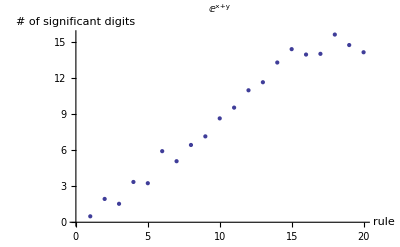

```mathematica
ClearAll[p,fun,a00,x,y,q,w]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=Exp[x+y];
Print["Mathematica value = ",a00=NIntegrate[fun[{x,y}],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20]];
Table[
{q,w}=DunavantRule[rule,{{0,0},{1,0},{0,1}}];
-Log@Abs[(NIntegrateTriangleDunavantMethod[p,fun,{q,w}]-a00)/a00]/Log[10],
{rule,1,20}
]//ListPlot[#,AxesLabel->{"rule","# of significant digits"},AxesOrigin->{0,0},PlotLabel->fun[{x,y}]]&//Print;
```

Arcsinh method single triangle
	source triangle
	near-singular field point

Mathematica value=0.023963917173953-0.6902623825876617 ⅈ

best value=0.0239639-0.690262 ⅈ

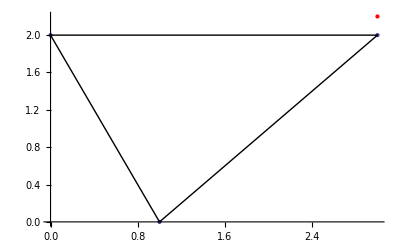

-Graphics3D-

```mathematica
ClearAll[P, P0,A, s1, s2, s3, wP, quadrules, iP]
P = {{1,0},{3,2},{0,2}} // N // ToPackedArray;
P0 = {3,2.2} // N // ToPackedArray;
A=Det[{P⟦2⟧-P⟦1⟧,P⟦3⟧-P⟦1⟧}];
s1 = A Det[{P[[1]] - P0, P[[2]] - P[[1]]}]>0;
s2 = A Det[{P[[2]] - P0, P[[3]] - P[[2]]}]>0;
s3 = A Det[{P[[3]] - P0, P[[1]] - P[[3]]}]>0;
wP = {1, 1, 1} // N // ToPackedArray;
If[!s1,wP⟦1⟧=-1.0];
If[!s2,wP⟦2⟧=-1.0];
If[!s3,wP⟦3⟧=-1.0];

ClearAll[fun, x, y, a0,a00]
fun[{x_, y_}] := Exp[ⅈ(x + 2y)];
raw = Table[
   quadrules = {LegendreRule[Nu, 0, 1], LegendreRule[Nv, 0, 1]};
   iP =
    {NIntegrateTriangleArcSinhMethod[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[3]], P[[1]]}, fun, quadrules]};
   a1 = iP.wP;
   {Nu, Nv, a1}
   ,
   {Nu, 30}, {Nv, 10}];
a00=NIntegrate[fun[{x,y}]/Norm[{x,y}-P0],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->16];
a0 = raw[[-1,-1, 3]];
Print["Mathematica value=",a00];
Print["best value=", a0];
data = {#[[1]], #[[2]], -Log@Abs[(#[[3]] - a0)/a0]/Log[10]} & /@ Flatten[raw, 1];
ListPlot[{P, {P0}}, PlotStyle -> {PointSize[Large], Red}, Epilog -> {Black, Line[P], Line[{P[[3]], P[[1]]}]}]
ListPlot3D[data, AxesLabel -> {"Nu", "Nv", "# of SD"}, PlotLabel -> fun[{x, y}],PlotRange->All,ImageSize -> Large]
```

Duffy - Only singular

In pt⟦np⟧: False

r={0.5,0.3}

cntr⟦np⟧={0.151174,0.758632}

|r-rp|≃0.576214

best value for m=0 is: 0.013379

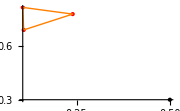
-Graphics-
-Graphics3D-

```mathematica
ClearAll[m,np,q,w,point,xx,data]
pStd={{0,0},{1,0},{0,1}};
m=0;
np=1;
point={0.5,0.3};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
data=Table[{q,w}=QuadratureProduct2D[LegendreRule[n2,0,1],LegendreRule[n1,0,1]];
xx=0.0;
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,1⟧,pt⟦np,2⟧},VscnmFuncR[m,point,#]&,{q,w}];
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,2⟧,pt⟦np,3⟧},VscnmFuncR[m,point,#]&,{q,w}];
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,3⟧,pt⟦np,1⟧},VscnmFuncR[m,point,#]&,{q,w}];
{n1,n2,xx},{n1,30},{n2,30}]//Flatten[#,1]&;
Print["best value for m=",m," is: ",data⟦-1,3⟧];
Print@TableForm@{
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->Small],
({#⟦1⟧,#⟦2⟧,-Log@Abs[#⟦3⟧-data⟦-1,3⟧]/Log[10]}&/@data)//ListPlot3D[#,PlotLabel->"DUFFY-SINGULAR "<>"m="<>ToString[m],AxesLabel->{"# of points","# of significant digits"},AxesOrigin->{0,0},ImageSize->Large]&};
```

Arcsinh method: Singular and near-singular and non-singular
Dunavant methods: Non-singular

In pt⟦np⟧: False

r={0.9,0.8}

cntr⟦np⟧={0.186399,0.306567}

|r-rp|≃0.867585

Rc = 0.0715497

best value for m= 40 is: 0.000176952+0.000298494 ⅈ

most # of SD by arcsinh = 6.46466 with 702 sampling points

most # of SD by Dunavant = 13.2249 with 79 sampling points

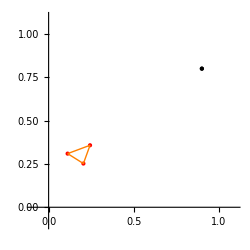
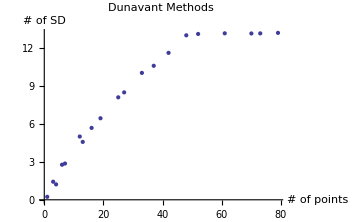
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
ClearAll[m,np,point,a0,a1]
m=40;
np=23;
point={0.9,0.8};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
Print["Rc = ",Rc⟦np⟧];
a0=NIntegrateTriangleArcSinh2[point,pt⟦np⟧,VscnmFuncR[m,point,#]&,{LegendreRule[100,0,1],LegendreRule[100,0,1]}];
raw1=Table[a1=NIntegrateTriangleArcSinh2[point,pt⟦np⟧,VscnmFuncR[m,point,#]&,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,a1},{Nu,1.2m+30},{Nv,3}]//Flatten[#,1]&;
data1={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw1;
raw2=Table[quadrules=DunavantRule[rule,{{0,0},{1,0},{0,1}}];{Length[quadrules⟦1⟧],NIntegrateTriangleDunavantMethod[pt⟦np⟧,VscnmFunc[m,point,#]&,quadrules]},{rule,1,20}];
data2={#⟦1⟧,-Log@Abs[(#⟦2⟧-a0)/a0]/Log[10]}&/@raw2;
Print["best value for m= ",m," is: ",a0];
Print["most # of SD by arcsinh = ",data1⟦-1,-1⟧," with ",3data1⟦-1,1⟧data1⟦-1,2⟧," sampling points"];
Print["most # of SD by Dunavant = ",data2⟦-1,-1⟧," with ",data2⟦-1,1⟧," sampling points"];
Print@{Show[
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->250,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AspectRatio->1]
],
ListPlot3D[data1,PlotRange->All,AxesLabel->{"Nu","Nv","# of SD"},PlotLabel->"ArcSinh Method",ImageSize->Medium],
ListPlot[data2,AxesLabel->{"# of points","# of SD"},PlotLabel->"Dunavant Methods",ImageSize->Medium]
}
```

Test the continuity of arcsinh method

```mathematica
ClearAll[quadrules,P,m,raw,xrange,yrange]
quadrules={LegendreRule[20,0,1],LegendreRule[4,0,1]};
P={{2,0},{3,2},{0,2}} // N // ToPackedArray;
m=0;
xrange=Range[0.001,3.0,0.03];
yrange=Range[-0.301,3.01,0.03];
raw=Table[{x,y,NIntegrateTriangleArcSinh2[{x,y},P,VscnmFuncR[m,{x,y},#]&,quadrules]},{y,yrange},{x,xrange}]//Flatten[#,1]&;
ListPlot3D[raw,InterpolationOrder->3,ImageSize->Large]
```

-Graphics3D-

Set::shape: Lists {qx$36311, qy$36311, w$36311} and $Failed[5, {{-1, -1}, {1, -1}, {-1, 1}}] are not the same shape.

Transpose::nmtx: The first two levels of the one-dimensional list {qx$36311, qy$36311} cannot be transposed.

12.3457

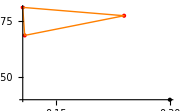

Transpose::nmtx: The first two levels of the one-dimensional list {0.108253  + 0.131305\ qx$36311 - 0.00254184\ qy$36311, 0.6875  + 0.0880791\ qx$36311 + 0.125316\ qy$36311} cannot be transposed.

Part::partd: Part specification w$36311 ⟦ 1 ⟧ is longer than depth of object.

CompiledFunction::cfsa: Argument ArcTan[0.191747  - 0.131305\ qx$36311 + 0.00254184\ qy$36311, -0.2875 - 0.0880791\ qx$36311 - 0.125316\ qy$36311] at position 1 should be a "machine-size real number".

Transpose::nmtx: The first two levels of the one-dimensional list {0.108253  + 0.114212\ qx$36311 + 0.131305\ qy$36311, 0.6875  - 0.0349203\ qx$36311 + 0.0880791\ qy$36311} cannot be transposed.

Part::partd: Part specification w$36311 ⟦ 1 ⟧ is longer than depth of object.

CompiledFunction::cfsa: Argument ArcTan[0.191747  - 0.114212\ qx$36311 - 0.131305\ qy$36311, -0.2875 + 0.0349203\ qx$36311 - 0.0880791\ qy$36311] at position 1 should be a "machine-size real number".

Transpose::nmtx: The first two levels of the one-dimensional list {0.885074  - 0.0720959\ qx$36311 - 0.135445\ qy$36311, 0.324683  + 0.128746\ qx$36311 + 0.0238156\ qy$36311} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Part::partd: Part specification w$36311 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

CompiledFunction::cfsa: Argument ArcTan[-0.585074 + 0.0720959\ qx$36311 + 0.135445\ qy$36311, 0.0753173  - 0.128746\ qx$36311 - 0.0238156\ qy$36311] at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.111585,0.30956},{0.204326,0.252314}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.111585,0.30956},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.116924,0.433247},{0.111585,0.30956}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.116924,0.433247},{0.22717,0.47703}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.116924,0.433247},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.135953,0.562576},{0.116924,0.433247}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.135953,0.562576},{0.22717,0.47703}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.204326,0.252314},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.204326,0.252314},{0.251036,0.174645}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.204326,0.252314},{0.31474,0.252306}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.22717,0.47703},{0.116924,0.433247}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.22717,0.47703},{0.135953,0.562576}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.22717,0.47703},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.22717,0.47703},{0.27293,0.566531}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.22717,0.47703},{0.327459,0.456879}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.111585,0.30956}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.116924,0.433247}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.204326,0.252314}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.22717,0.47703}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.31474,0.252306}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.327459,0.456879}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.243285,0.357826},{0.377294,0.349159}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.251036,0.174645},{0.31474,0.252306}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.251036,0.174645},{0.375,0.17524}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.27293,0.566531},{0.135953,0.562576}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.27293,0.566531},{0.22717,0.47703}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.27293,0.566531},{0.327459,0.456879}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.31474,0.252306},{0.204326,0.252314}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.31474,0.252306},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.31474,0.252306},{0.251036,0.174645}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.31474,0.252306},{0.375,0.17524}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.31474,0.252306},{0.377294,0.349159}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.31474,0.252306},{0.4375,0.242228}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.327459,0.456879},{0.22717,0.47703}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.327459,0.456879},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.327459,0.456879},{0.27293,0.566531}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.327459,0.456879},{0.377294,0.349159}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.327459,0.456879},{0.381148,0.566858}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.327459,0.456879},{0.439451,0.458402}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.375,0.17524},{0.31474,0.252306}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.375,0.17524},{0.4375,0.242228}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.377294,0.349159},{0.243285,0.357826}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.377294,0.349159},{0.31474,0.252306}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.377294,0.349159},{0.327459,0.456879}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.377294,0.349159},{0.4375,0.242228}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.377294,0.349159},{0.439451,0.458402}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.377294,0.349159},{0.500017,0.350491}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.381148,0.566858},{0.27293,0.566531}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.381148,0.566858},{0.327459,0.456879}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.381148,0.566858},{0.439451,0.458402}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.4375,0.242228},{0.31474,0.252306}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.4375,0.242228},{0.377294,0.349159}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.4375,0.242228},{0.500017,0.350491}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.439451,0.458402},{0.327459,0.456879}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.439451,0.458402},{0.377294,0.349159}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.439451,0.458402},{0.381148,0.566858}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.439451,0.458402},{0.500136,0.567072}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]-1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.500017,0.350491},{0.377294,0.349159}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.500017,0.350491},{0.439451,0.458402}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+1. NIntegrateTriangleArcSinhMethod[{{0.3,0.4},{0.500136,0.567072},{0.381148,0.566858}},VscnmFuncR[m,P,#1]&,{$Failed[8,0,1],$Failed[3,0,1]}]+(0.000201896 ⅇ^(0.-0.0915064 qx$36311-0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.0915064 qx$36311-0.125 qy$36311))/(√((-0.6+0.0915064 qx$36311)^2+(0.3-0.0915064 qx$36311-0.125 qy$36311)^2))) √(Abs[-0.6+0.0915064 qx$36311]^2+Abs[0.3-0.0915064 qx$36311-0.125 qy$36311]^2))+(0.000258133 ⅇ^(0.-0.116995 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.116995 qx$36311))/(√((0.3-0.116995 qx$36311)^2+(0.275-0.0612423 qx$36311-0.125 qy$36311)^2))) √(Abs[0.3-0.116995 qx$36311]^2+Abs[0.275-0.0612423 qx$36311-0.125 qy$36311]^2))+(0.000246196 ⅇ^(0.-0.111585 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.111585 qx$36311))/(√((0.3-0.111585 qx$36311)^2+(0.15-0.0595602 qx$36311-0.125 qy$36311)^2))) √(Abs[0.3-0.111585 qx$36311]^2+Abs[0.15-0.0595602 qx$36311-0.125 qy$36311]^2))+(0.000238845 ⅇ^(-0.375-0.0625 qx$36311-0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.075-0.0625 qx$36311-0.125 qy$36311))/(√((-0.6+0.108253 qx$36311)^2+(-0.075-0.0625 qx$36311-0.125 qy$36311)^2))) √(Abs[-0.6+0.108253 qx$36311]^2+Abs[-0.075-0.0625 qx$36311-0.125 qy$36311]^2))+(0.000201896 ⅇ^(0.-0.0915064 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.0915064 qx$36311))/(√((0.3-0.0915064 qx$36311)^2+(-0.475-0.0334936 qx$36311-0.125 qy$36311)^2))) √(Abs[0.3-0.0915064 qx$36311]^2+Abs[-0.475-0.0334936 qx$36311-0.125 qy$36311]^2))+(0.000226873 ⅇ^(-0.75-0.0588666 qx$36311-0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.45-0.0588666 qx$36311-0.125 qy$36311))/(√((-0.6+0.102827 qx$36311)^2+(-0.45-0.0588666 qx$36311-0.125 qy$36311)^2))) √(Abs[-0.6+0.102827 qx$36311]^2+Abs[-0.45-0.0588666 qx$36311-0.125 qy$36311]^2))+(0.000237024 ⅇ^(-0.625-0.0642388 qx$36311-0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325-0.0642388 qx$36311-0.125 qy$36311))/(√((-0.6+0.107428 qx$36311)^2+(-0.325-0.0642388 qx$36311-0.125 qy$36311)^2))) √(Abs[-0.6+0.107428 qx$36311]^2+Abs[-0.325-0.0642388 qx$36311-0.125 qy$36311]^2))+(0.00029996 ⅇ^(0.-0.135953 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.135953 qx$36311))/(√((0.3-0.135953 qx$36311)^2+(-0.1-0.0625759 qx$36311-0.125 qy$36311)^2))) √(Abs[0.3-0.135953 qx$36311]^2+Abs[-0.1-0.0625759 qx$36311-0.125 qy$36311]^2))+(0.000258494 ⅇ^(-0.108253-0.114212 qx$36311-0.131305 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.191747-0.114212 qx$36311-0.131305 qy$36311))/(√((0.191747-0.114212 qx$36311-0.131305 qy$36311)^2+(-0.2875+0.0349203 qx$36311-0.0880791 qy$36311)^2))) √(Abs[0.191747-0.114212 qx$36311-0.131305 qy$36311]^2+Abs[-0.2875+0.0349203 qx$36311-0.0880791 qy$36311]^2))+(0.000211567 ⅇ^(-0.135953-0.136977 qx$36311-0.0865119 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.164047-0.136977 qx$36311-0.0865119 qy$36311))/(√((-0.162576-0.00395563 qx$36311-0.0900038 qy$36311)^2+(0.164047-0.136977 qx$36311-0.0865119 qy$36311)^2))) √(Abs[-0.162576-0.00395563 qx$36311-0.0900038 qy$36311]^2+Abs[0.164047-0.136977 qx$36311-0.0865119 qy$36311]^2))+(0.000167914 ⅇ^(-0.8125-0.0959936 qx$36311-0.0864818 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.5125-0.0959936 qx$36311-0.0864818 qy$36311))/(√((-0.5125-0.0959936 qx$36311-0.0864818 qy$36311)^2+(0.291747+0.0167468 qx$36311-0.084014 qy$36311)^2))) √(Abs[-0.5125-0.0959936 qx$36311-0.0864818 qy$36311]^2+Abs[0.291747+0.0167468 qx$36311-0.084014 qy$36311]^2))+(0.000212403 ⅇ^(-0.125-0.125 qx$36311-0.0661089 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.175-0.125 qx$36311-0.0661089 qy$36311))/(√((0.4-0.0962686 qy$36311)^2+(0.175-0.125 qx$36311-0.0661089 qy$36311)^2))) √(Abs[0.4-0.0962686 qy$36311]^2+Abs[0.175-0.125 qx$36311-0.0661089 qy$36311]^2))+(0.000242145 ⅇ^(-0.500136-0.126088 qx$36311-0.0639469 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200136-0.126088 qx$36311-0.0639469 qy$36311))/(√((-0.167072-0.000679165 qx$36311-0.109146 qy$36311)^2+(-0.200136-0.126088 qx$36311-0.0639469 qy$36311)^2))) √(Abs[-0.167072-0.000679165 qx$36311-0.109146 qy$36311]^2+Abs[-0.200136-0.126088 qx$36311-0.0639469 qy$36311]^2))+(0.000240327 ⅇ^(-0.562651-0.125004 qx$36311-0.0635729 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.262651-0.125004 qx$36311-0.0635729 qy$36311))/(√((-0.0588285-2.34204×10^-6 qx$36311-0.108923 qy$36311)^2+(-0.262651-0.125004 qx$36311-0.0635729 qy$36311)^2))) √(Abs[-0.0588285-2.34204×10^-6 qx$36311-0.108923 qy$36311]^2+Abs[-0.262651-0.125004 qx$36311-0.0635729 qy$36311]^2))+(0.000217599 ⅇ^(-0.25-0.125 qx$36311-0.0632961 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.05-0.125 qx$36311-0.0632961 qy$36311))/(√((0.4-0.0986236 qy$36311)^2+(0.05-0.125 qx$36311-0.0632961 qy$36311)^2))) √(Abs[0.4-0.0986236 qy$36311]^2+Abs[0.05-0.125 qx$36311-0.0632961 qy$36311]^2))+(0.000236645 ⅇ^(0.-0.108253 qx$36311-0.105711 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.108253 qx$36311-0.105711 qy$36311))/(√((0.3-0.108253 qx$36311-0.105711 qy$36311)^2+(-0.35+0.0625 qx$36311-0.0628161 qy$36311)^2))) √(Abs[0.3-0.108253 qx$36311-0.105711 qy$36311]^2+Abs[-0.35+0.0625 qx$36311-0.0628161 qy$36311]^2))+(0.000238995 ⅇ^(-0.500021-0.124979 qx$36311-0.0626717 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200021-0.124979 qx$36311-0.0626717 qy$36311))/(√((-0.383504+0.0000101904 qx$36311-0.108335 qy$36311)^2+(-0.200021-0.124979 qx$36311-0.0626717 qy$36311)^2))) √(Abs[-0.383504+0.0000101904 qx$36311-0.108335 qy$36311]^2+Abs[-0.200021-0.124979 qx$36311-0.0626717 qy$36311]^2))+(0.000240492 ⅇ^(-0.625019-0.12461 qx$36311-0.0626362 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325019-0.12461 qx$36311-0.0626362 qy$36311))/(√((0.0495074+0.00199435 qx$36311-0.108338 qy$36311)^2+(-0.325019-0.12461 qx$36311-0.0626362 qy$36311)^2))) √(Abs[0.0495074+0.00199435 qx$36311-0.108338 qy$36311]^2+Abs[-0.325019-0.12461 qx$36311-0.0626362 qy$36311]^2))+(0.000289329 ⅇ^(0.-0.116924 qx$36311-0.135953 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.116924 qx$36311-0.135953 qy$36311))/(√((0.3-0.116924 qx$36311-0.135953 qy$36311)^2+(-0.1+0.0667526 qx$36311-0.0625759 qy$36311)^2))) √(Abs[0.3-0.116924 qx$36311-0.135953 qy$36311]^2+Abs[-0.1+0.0667526 qx$36311-0.0625759 qy$36311]^2))+(0.000238868 ⅇ^(-0.4375-0.125 qx$36311-0.0625168 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375-0.125 qx$36311-0.0625168 qy$36311))/(√((0.157772-9.25926×10^-14 qx$36311-0.108264 qy$36311)^2+(-0.1375-0.125 qx$36311-0.0625168 qy$36311)^2))) √(Abs[0.157772-9.25926×10^-14 qx$36311-0.108264 qy$36311]^2+Abs[-0.1375-0.125 qx$36311-0.0625168 qy$36311]^2))+(0.000147798 ⅇ^(-0.4375-0.125 qx$36311-0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375-0.125 qx$36311-0.0625 qy$36311))/(√((0.291747-4.21052×10^-14 qx$36311-0.0669873 qy$36311)^2+(-0.1375-0.125 qx$36311-0.0625 qy$36311)^2))) √(Abs[0.291747-4.21052×10^-14 qx$36311-0.0669873 qy$36311]^2+Abs[-0.1375-0.125 qx$36311-0.0625 qy$36311]^2))+(0.000238845 ⅇ^(-0.625-0.125 qx$36311-0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325-0.125 qx$36311-0.0625 qy$36311))/(√((0.4-0.108253 qy$36311)^2+(-0.325-0.125 qx$36311-0.0625 qy$36311)^2))) √(Abs[0.4-0.108253 qy$36311]^2+Abs[-0.325-0.125 qx$36311-0.0625 qy$36311]^2))+(0.000238845 ⅇ^(-0.5-0.125 qx$36311-0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2-0.125 qx$36311-0.0625 qy$36311))/(√((0.4-0.108253 qy$36311)^2+(-0.2-0.125 qx$36311-0.0625 qy$36311)^2))) √(Abs[0.4-0.108253 qy$36311]^2+Abs[-0.2-0.125 qx$36311-0.0625 qy$36311]^2))+(0.000269258 ⅇ^(0.-0.135953 qx$36311-0.108253 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.135953 qx$36311-0.108253 qy$36311))/(√((0.3-0.135953 qx$36311-0.108253 qy$36311)^2+(-0.225+0.0624241 qx$36311-0.0625 qy$36311)^2))) √(Abs[0.3-0.135953 qx$36311-0.108253 qy$36311]^2+Abs[-0.225+0.0624241 qx$36311-0.0625 qy$36311]^2))+(0.000245193 ⅇ^(-0.687655-0.125323 qx$36311-0.0623451 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.387655-0.125323 qx$36311-0.0623451 qy$36311))/(√((-0.0588308+0.00540169 qx$36311-0.108157 qy$36311)^2+(-0.387655-0.125323 qx$36311-0.0623451 qy$36311)^2))) √(Abs[-0.0588308+0.00540169 qx$36311-0.108157 qy$36311]^2+Abs[-0.387655-0.125323 qx$36311-0.0623451 qy$36311]^2))+(0.000234045 ⅇ^(-0.698516-0.123082 qx$36311-0.0617053 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.398516-0.123082 qx$36311-0.0617053 qy$36311))/(√((-0.282117+0.00362477 qx$36311-0.105914 qy$36311)^2+(-0.398516-0.123082 qx$36311-0.0617053 qy$36311)^2))) √(Abs[-0.282117+0.00362477 qx$36311-0.105914 qy$36311]^2+Abs[-0.398516-0.123082 qx$36311-0.0617053 qy$36311]^2))+(0.000168083 ⅇ^(0.-0.0915064 qx$36311-0.116995 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.0915064 qx$36311-0.116995 qy$36311))/(√((0.3-0.0915064 qx$36311-0.116995 qy$36311)^2+(0.275+0.0334936 qx$36311-0.0612423 qy$36311)^2))) √(Abs[0.3-0.0915064 qx$36311-0.116995 qy$36311]^2+Abs[0.275+0.0334936 qx$36311-0.0612423 qy$36311]^2))+(0.000221903 ⅇ^(-0.689239-0.119628 qx$36311-0.0607612 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.389239-0.119628 qx$36311-0.0607612 qy$36311))/(√((-0.492572-0.00460084 qx$36311-0.107428 qy$36311)^2+(-0.389239-0.119628 qx$36311-0.0607612 qy$36311)^2))) √(Abs[-0.492572-0.00460084 qx$36311-0.107428 qy$36311]^2+Abs[-0.389239-0.119628 qx$36311-0.0607612 qy$36311]^2))+(0.000248571 ⅇ^(0.-0.116995 qx$36311-0.111585 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.116995 qx$36311-0.111585 qy$36311))/(√((0.3-0.116995 qx$36311-0.111585 qy$36311)^2+(0.15+0.0637577 qx$36311-0.0595602 qy$36311)^2))) √(Abs[0.3-0.116995 qx$36311-0.111585 qy$36311]^2+Abs[0.15+0.0637577 qx$36311-0.0595602 qy$36311]^2))+(0.000143941 ⅇ^(-0.625-0.106521 qx$36311-0.0588978 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325-0.106521 qx$36311-0.0588978 qy$36311))/(√((0.22476-0.000574474 qx$36311-0.076874 qy$36311)^2+(-0.325-0.106521 qx$36311-0.0588978 qy$36311)^2))) √(Abs[0.22476-0.000574474 qx$36311-0.076874 qy$36311]^2+Abs[-0.325-0.106521 qx$36311-0.0588978 qy$36311]^2))+(0.000249777 ⅇ^(0.-0.111585 qx$36311-0.116924 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.111585 qx$36311-0.116924 qy$36311))/(√((0.3-0.111585 qx$36311-0.116924 qy$36311)^2+(0.025+0.0654398 qx$36311-0.0582474 qy$36311)^2))) √(Abs[0.3-0.111585 qx$36311-0.116924 qy$36311]^2+Abs[0.025+0.0654398 qx$36311-0.0582474 qy$36311]^2))+(0.000149065 ⅇ^(-0.6875-0.125 qx$36311-0.0440215 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.3875-0.125 qx$36311-0.0440215 qy$36311))/(√((0.291747-5.19029×10^-14 qx$36311-0.0675618 qy$36311)^2+(-0.3875-0.125 qx$36311-0.0440215 qy$36311)^2))) √(Abs[0.291747-5.19029×10^-14 qx$36311-0.0675618 qy$36311]^2+Abs[-0.3875-0.125 qx$36311-0.0440215 qy$36311]^2))+(0.000201896 ⅇ^(-0.875-0.125 qx$36311-0.0334936 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.575-0.125 qx$36311-0.0334936 qy$36311))/(√((0.4-0.0915064 qy$36311)^2+(-0.575-0.125 qx$36311-0.0334936 qy$36311)^2))) √(Abs[0.4-0.0915064 qy$36311]^2+Abs[-0.575-0.125 qx$36311-0.0334936 qy$36311]^2))+(0.000162933 ⅇ^(0.-0.105711 qx$36311-0.0915064 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.105711 qx$36311-0.0915064 qy$36311))/(√((0.3-0.105711 qx$36311-0.0915064 qy$36311)^2+(-0.475+0.0621839 qx$36311-0.0334936 qy$36311)^2))) √(Abs[0.3-0.105711 qx$36311-0.0915064 qy$36311]^2+Abs[-0.475+0.0621839 qx$36311-0.0334936 qy$36311]^2))+(0.000205106 ⅇ^(-0.890099-0.109901 qx$36311-0.0325635 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590099-0.109901 qx$36311-0.0325635 qy$36311))/(√((-0.163563-0.0614368 qx$36311-0.123937 qy$36311)^2+(-0.590099-0.109901 qx$36311-0.0325635 qy$36311)^2))) √(Abs[-0.163563-0.0614368 qx$36311-0.123937 qy$36311]^2+Abs[-0.590099-0.109901 qx$36311-0.0325635 qy$36311]^2))+(0.000217861 ⅇ^(-0.222465-0.103543 qx$36311-0.0170932 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.0775353-0.103543 qx$36311-0.0170932 qy$36311))/(√((-0.25258-0.0229839 qx$36311-0.122999 qy$36311)^2+(0.0775353-0.103543 qx$36311-0.0170932 qy$36311)^2))) √(Abs[-0.25258-0.0229839 qx$36311-0.122999 qy$36311]^2+Abs[0.0775353-0.103543 qx$36311-0.0170932 qy$36311]^2))+(0.000154445 ⅇ^(-0.5625-0.0625 qx$36311-0.121398 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2625-0.0625 qx$36311-0.121398 qy$36311))/(√((-0.2625-0.0625 qx$36311-0.121398 qy$36311)^2+(0.157772+0.0669873 qx$36311-0.00988675 qy$36311)^2))) √(Abs[-0.2625-0.0625 qx$36311-0.121398 qy$36311]^2+Abs[0.157772+0.0669873 qx$36311-0.00988675 qy$36311]^2))+(0.000226701 ⅇ^(-0.313296-0.0617039 qx$36311-0.124204 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.0132961-0.0617039 qx$36311-0.124204 qy$36311))/(√((-0.0132961-0.0617039 qx$36311-0.124204 qy$36311)^2+(0.301376+0.0986236 qx$36311-0.00962958 qy$36311)^2))) √(Abs[-0.0132961-0.0617039 qx$36311-0.124204 qy$36311]^2+Abs[0.301376+0.0986236 qx$36311-0.00962958 qy$36311]^2))+(0.000226508 ⅇ^(-0.689239-0.0709825 qx$36311-0.119628 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.389239-0.0709825 qx$36311-0.119628 qy$36311))/(√((-0.389239-0.0709825 qx$36311-0.119628 qy$36311)^2+(-0.492572+0.104542 qx$36311-0.00460084 qy$36311)^2))) √(Abs[-0.389239-0.0709825 qx$36311-0.119628 qy$36311]^2+Abs[-0.492572+0.104542 qx$36311-0.00460084 qy$36311]^2))+(0.000241652 ⅇ^(-0.500136-0.0625151 qx$36311-0.126088 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200136-0.0625151 qx$36311-0.126088 qy$36311))/(√((-0.200136-0.0625151 qx$36311-0.126088 qy$36311)^2+(-0.167072+0.108244 qx$36311-0.000679165 qy$36311)^2))) √(Abs[-0.200136-0.0625151 qx$36311-0.126088 qy$36311]^2+Abs[-0.167072+0.108244 qx$36311-0.000679165 qy$36311]^2))+(0.000239293 ⅇ^(-0.4375-0.0625215 qx$36311-0.125193 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375-0.0625215 qx$36311-0.125193 qy$36311))/(√((-0.1375-0.0625215 qx$36311-0.125193 qy$36311)^2+(-0.491747+0.108243 qx$36311-0.0000917135 qy$36311)^2))) √(Abs[-0.1375-0.0625215 qx$36311-0.125193 qy$36311]^2+Abs[-0.491747+0.108243 qx$36311-0.0000917135 qy$36311]^2))+(0.000239037 ⅇ^(-0.562651-0.0623675 qx$36311-0.125004 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.262651-0.0623675 qx$36311-0.125004 qy$36311))/(√((-0.262651-0.0623675 qx$36311-0.125004 qy$36311)^2+(-0.0588285+0.108336 qx$36311-2.34204×10^-6 qy$36311)^2))) √(Abs[-0.262651-0.0623675 qx$36311-0.125004 qy$36311]^2+Abs[-0.0588285+0.108336 qx$36311-2.34204×10^-6 qy$36311]^2))+(0.000238873 ⅇ^(-0.500017-0.0624832 qx$36311-0.125002 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200017-0.0624832 qx$36311-0.125002 qy$36311))/(√((-0.200017-0.0624832 qx$36311-0.125002 qy$36311)^2+(0.0495086+0.108264 qx$36311-1.16455×10^-6 qy$36311)^2))) √(Abs[-0.200017-0.0624832 qx$36311-0.125002 qy$36311]^2+Abs[0.0495086+0.108264 qx$36311-1.16455×10^-6 qy$36311]^2))+(0.000238845 ⅇ^(-0.5625-0.0625 qx$36311-0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2625-0.0625 qx$36311-0.125 qy$36311))/(√((-0.2625-0.0625 qx$36311-0.125 qy$36311)^2+(0.291747+0.108253 qx$36311-2.46594×10^-13 qy$36311)^2))) √(Abs[-0.2625-0.0625 qx$36311-0.125 qy$36311]^2+Abs[0.291747+0.108253 qx$36311-2.46594×10^-13 qy$36311]^2))+(0.000236657 ⅇ^(-0.500021-0.0640615 qx$36311-0.124979 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200021-0.0640615 qx$36311-0.124979 qy$36311))/(√((-0.200021-0.0640615 qx$36311-0.124979 qy$36311)^2+(-0.383504+0.107285 qx$36311+0.0000101904 qy$36311)^2))) √(Abs[-0.200021-0.0640615 qx$36311-0.124979 qy$36311]^2+Abs[-0.383504+0.107285 qx$36311+0.0000101904 qy$36311]^2))+(0.000240405 ⅇ^(-0.439349-0.0607872 qx$36311-0.124734 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.139349-0.0607872 qx$36311-0.124734 qy$36311))/(√((-0.139349-0.0607872 qx$36311-0.124734 qy$36311)^2+(-0.276308+0.109236 qx$36311+0.0000897172 qy$36311)^2))) √(Abs[-0.139349-0.0607872 qx$36311-0.124734 qy$36311]^2+Abs[-0.276308+0.109236 qx$36311+0.0000897172 qy$36311]^2))+(0.000214307 ⅇ^(-0.625019-0.0588791 qx$36311-0.12461 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325019-0.0588791 qx$36311-0.12461 qy$36311))/(√((-0.325019-0.0588791 qx$36311-0.12461 qy$36311)^2+(0.0495074+0.0983781 qx$36311+0.00199435 qy$36311)^2))) √(Abs[-0.325019-0.0588791 qx$36311-0.12461 qy$36311]^2+Abs[0.0495074+0.0983781 qx$36311+0.00199435 qy$36311]^2))+(0.000153179 ⅇ^(-0.683898-0.0476237 qx$36311-0.115013 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.383898-0.0476237 qx$36311-0.115013 qy$36311))/(√((-0.383898-0.0476237 qx$36311-0.115013 qy$36311)^2+(0.147885+0.0762996 qx$36311+0.00204117 qy$36311)^2))) √(Abs[-0.383898-0.0476237 qx$36311-0.115013 qy$36311]^2+Abs[0.147885+0.0762996 qx$36311+0.00204117 qy$36311]^2))+(0.000294389 ⅇ^(-0.108253-0.131305 qx$36311+0.00254184 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.191747-0.131305 qx$36311+0.00254184 qy$36311))/(√((-0.2875-0.0880791 qx$36311-0.125316 qy$36311)^2+(0.191747-0.131305 qx$36311+0.00254184 qy$36311)^2))) √(Abs[-0.2875-0.0880791 qx$36311-0.125316 qy$36311]^2+Abs[0.191747-0.131305 qx$36311+0.00254184 qy$36311]^2))+(0.000261452 ⅇ^(-0.18858-0.0509782 qx$36311-0.12404 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.11142-0.0509782 qx$36311-0.12404 qy$36311))/(√((0.11142-0.0509782 qx$36311-0.12404 qy$36311)^2+(-0.496866+0.121287 qx$36311+0.00455005 qy$36311)^2))) √(Abs[0.11142-0.0509782 qx$36311-0.12404 qy$36311]^2+Abs[-0.496866+0.121287 qx$36311+0.00455005 qy$36311]^2))+(0.000238153 ⅇ^(-0.687655-0.0619738 qx$36311-0.125323 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.387655-0.0619738 qx$36311-0.125323 qy$36311))/(√((-0.387655-0.0619738 qx$36311-0.125323 qy$36311)^2+(-0.0588308+0.110333 qx$36311+0.00540169 qy$36311)^2))) √(Abs[-0.387655-0.0619738 qx$36311-0.125323 qy$36311]^2+Abs[-0.0588308+0.110333 qx$36311+0.00540169 qy$36311]^2))+(0.000236637 ⅇ^(-0.8125-0.0864818 qx$36311+0.0135889 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.5125-0.0864818 qx$36311+0.0135889 qy$36311))/(√((0.291747-0.084014 qx$36311-0.14182 qy$36311)^2+(-0.5125-0.0864818 qx$36311+0.0135889 qy$36311)^2))) √(Abs[0.291747-0.084014 qx$36311-0.14182 qy$36311]^2+Abs[-0.5125-0.0864818 qx$36311+0.0135889 qy$36311]^2))+(0.000161021 ⅇ^(-0.105711-0.0828684 qx$36311+0.014205 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.194289-0.0828684 qx$36311+0.014205 qy$36311))/(√((-0.412816-0.0840495 qx$36311-0.0956776 qy$36311)^2+(0.194289-0.0828684 qx$36311+0.014205 qy$36311)^2))) √(Abs[-0.412816-0.0840495 qx$36311-0.0956776 qy$36311]^2+Abs[0.194289-0.0828684 qx$36311+0.014205 qy$36311]^2))+(0.00016369 ⅇ^(-0.125-0.0661089 qx$36311+0.0334936 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.175-0.0661089 qx$36311+0.0334936 qy$36311))/(√((0.4-0.0962686 qx$36311-0.0915064 qy$36311)^2+(0.175-0.0661089 qx$36311+0.0334936 qy$36311)^2))) √(Abs[0.4-0.0962686 qx$36311-0.0915064 qy$36311]^2+Abs[0.175-0.0661089 qx$36311+0.0334936 qy$36311]^2))+(0.000201896 ⅇ^(0.-0.0915064 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.0915064 qy$36311))/(√((0.3-0.0915064 qy$36311)^2+(0.275+0.125 qx$36311+0.0334936 qy$36311)^2))) √(Abs[0.3-0.0915064 qy$36311]^2+Abs[0.275+0.125 qx$36311+0.0334936 qy$36311]^2))+(0.000234765 ⅇ^(-0.108253-0.0276996 qx$36311-0.114212 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.191747-0.0276996 qx$36311-0.114212 qy$36311))/(√((0.191747-0.0276996 qx$36311-0.114212 qy$36311)^2+(-0.2875+0.124924 qx$36311+0.0349203 qy$36311)^2))) √(Abs[0.191747-0.0276996 qx$36311-0.114212 qy$36311]^2+Abs[-0.2875+0.124924 qx$36311+0.0349203 qy$36311]^2))+(0.000246825 ⅇ^(-0.75-0.0715979 qx$36311+0.051484 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.45-0.0715979 qx$36311+0.051484 qy$36311))/(√((-0.166987-0.111505 qx$36311-0.11513 qy$36311)^2+(-0.45-0.0715979 qx$36311+0.051484 qy$36311)^2))) √(Abs[-0.166987-0.111505 qx$36311-0.11513 qy$36311]^2+Abs[-0.45-0.0715979 qx$36311+0.051484 qy$36311]^2))+(0.000191229 ⅇ^(-0.890925-0.031737 qx$36311-0.109075 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590925-0.031737 qx$36311-0.109075 qy$36311))/(√((-0.590925-0.031737 qx$36311-0.109075 qy$36311)^2+(-0.401939+0.114439 qx$36311+0.0519386 qy$36311)^2))) √(Abs[-0.590925-0.031737 qx$36311-0.109075 qy$36311]^2+Abs[-0.401939+0.114439 qx$36311+0.0519386 qy$36311]^2))+(0.0001964 ⅇ^(-0.111585-0.00541029 qx$36311-0.0927415 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.188415-0.00541029 qx$36311-0.0927415 qy$36311))/(√((0.188415-0.00541029 qx$36311-0.0927415 qy$36311)^2+(0.0904398+0.123318 qx$36311+0.0572464 qy$36311)^2))) √(Abs[0.188415-0.00541029 qx$36311-0.0927415 qy$36311]^2+Abs[0.0904398+0.123318 qx$36311+0.0572464 qy$36311]^2))+(0.000210071 ⅇ^(-0.25-0.0632961 qx$36311+0.0588911 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.05-0.0632961 qx$36311+0.0588911 qy$36311))/(√((0.4-0.0986236 qx$36311-0.0962686 qy$36311)^2+(0.05-0.0632961 qx$36311+0.0588911 qy$36311)^2))) √(Abs[0.4-0.0986236 qx$36311-0.0962686 qy$36311]^2+Abs[0.05-0.0632961 qx$36311+0.0588911 qy$36311]^2))+(0.000237136 ⅇ^(-0.687655-0.0623451 qx$36311+0.0614309 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.387655-0.0623451 qx$36311+0.0614309 qy$36311))/(√((-0.0588308-0.108157 qx$36311-0.108921 qy$36311)^2+(-0.387655-0.0623451 qx$36311+0.0614309 qy$36311)^2))) √(Abs[-0.0588308-0.108157 qx$36311-0.108921 qy$36311]^2+Abs[-0.387655-0.0623451 qx$36311+0.0614309 qy$36311]^2))+(0.000233237 ⅇ^(0.-0.105711 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.105711 qy$36311))/(√((0.3-0.105711 qy$36311)^2+(-0.475+0.125 qx$36311+0.0621839 qy$36311)^2))) √(Abs[0.3-0.105711 qy$36311]^2+Abs[-0.475+0.125 qx$36311+0.0621839 qy$36311]^2))+(0.000166995 ⅇ^(-0.313296-0.0617039 qx$36311+0.0622606 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.0132961-0.0617039 qx$36311+0.0622606 qy$36311))/(√((0.301376-0.0766169 qx$36311-0.0760214 qy$36311)^2+(-0.0132961-0.0617039 qx$36311+0.0622606 qy$36311)^2))) √(Abs[0.301376-0.0766169 qx$36311-0.0760214 qy$36311]^2+Abs[-0.0132961-0.0617039 qx$36311+0.0622606 qy$36311]^2))+(0.000147798 ⅇ^(-0.4375-0.0625 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375-0.0625 qx$36311+0.0625 qy$36311))/(√((0.291747-0.0669873 qx$36311-0.0669873 qy$36311)^2+(-0.1375-0.0625 qx$36311+0.0625 qy$36311)^2))) √(Abs[0.291747-0.0669873 qx$36311-0.0669873 qy$36311]^2+Abs[-0.1375-0.0625 qx$36311+0.0625 qy$36311]^2))+(0.000147798 ⅇ^(-0.5625-0.0625 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2625-0.0625 qx$36311+0.0625 qy$36311))/(√((0.291747-0.0669873 qx$36311-0.0669873 qy$36311)^2+(-0.2625-0.0625 qx$36311+0.0625 qy$36311)^2))) √(Abs[0.291747-0.0669873 qx$36311-0.0669873 qy$36311]^2+Abs[-0.2625-0.0625 qx$36311+0.0625 qy$36311]^2))+(0.000238845 ⅇ^(0.-0.108253 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.108253 qy$36311))/(√((0.3-0.108253 qy$36311)^2+(-0.35+0.125 qx$36311+0.0625 qy$36311)^2))) √(Abs[0.3-0.108253 qy$36311]^2+Abs[-0.35+0.125 qx$36311+0.0625 qy$36311]^2))+(0.000238845 ⅇ^(-0.5-0.0625 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2-0.0625 qx$36311+0.0625 qy$36311))/(√((0.4-0.108253 qx$36311-0.108253 qy$36311)^2+(-0.2-0.0625 qx$36311+0.0625 qy$36311)^2))) √(Abs[0.4-0.108253 qx$36311-0.108253 qy$36311]^2+Abs[-0.2-0.0625 qx$36311+0.0625 qy$36311]^2))+(0.000164946 ⅇ^(-0.875-0.0334936 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.575-0.0334936 qx$36311+0.0625 qy$36311))/(√((0.4-0.0915064 qx$36311-0.108253 qy$36311)^2+(-0.575-0.0334936 qx$36311+0.0625 qy$36311)^2))) √(Abs[0.4-0.0915064 qx$36311-0.108253 qy$36311]^2+Abs[-0.575-0.0334936 qx$36311+0.0625 qy$36311]^2))+(0.000126583 ⅇ^(-0.6875-0.0440215 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.3875-0.0440215 qx$36311+0.0625 qy$36311))/(√((0.291747-0.0675618 qx$36311-0.0669873 qy$36311)^2+(-0.3875-0.0440215 qx$36311+0.0625 qy$36311)^2))) √(Abs[0.291747-0.0675618 qx$36311-0.0669873 qy$36311]^2+Abs[-0.3875-0.0440215 qx$36311+0.0625 qy$36311]^2))+(0.000205618 ⅇ^(-0.890099-0.0267455 qx$36311-0.109901 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590099-0.0267455 qx$36311-0.109901 qy$36311))/(√((-0.590099-0.0267455 qx$36311-0.109901 qy$36311)^2+(-0.163563+0.121466 qx$36311+0.0635632 qy$36311)^2))) √(Abs[-0.590099-0.0267455 qx$36311-0.109901 qy$36311]^2+Abs[-0.163563+0.121466 qx$36311+0.0635632 qy$36311]^2))+(0.000257976 ⅇ^(0.-0.116924 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.3-0.116924 qy$36311))/(√((0.3-0.116924 qy$36311)^2+(-0.1+0.125 qx$36311+0.0667526 qy$36311)^2))) √(Abs[0.3-0.116924 qy$36311]^2+Abs[-0.1+0.125 qx$36311+0.0667526 qy$36311]^2))+(0.000147798 ⅇ^(-0.5625+0.125 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2625+0.125 qx$36311+0.0625 qy$36311))/(√((-0.2625+0.125 qx$36311+0.0625 qy$36311)^2+(0.157772+9.25926×10^-14 qx$36311+0.0669873 qy$36311)^2))) √(Abs[-0.2625+0.125 qx$36311+0.0625 qy$36311]^2+Abs[0.157772+9.25926×10^-14 qx$36311+0.0669873 qy$36311]^2))+(0.000147798 ⅇ^(-0.5625+0.0625 qx$36311-0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2625+0.0625 qx$36311-0.0625 qy$36311))/(√((-0.2625+0.0625 qx$36311-0.0625 qy$36311)^2+(0.157772+0.0669873 qx$36311+0.0669873 qy$36311)^2))) √(Abs[-0.2625+0.0625 qx$36311-0.0625 qy$36311]^2+Abs[0.157772+0.0669873 qx$36311+0.0669873 qy$36311]^2))+(0.00021591 ⅇ^(-0.890099-0.0325635 qx$36311+0.0685011 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590099-0.0325635 qx$36311+0.0685011 qy$36311))/(√((-0.163563-0.123937 qx$36311-0.114929 qy$36311)^2+(-0.590099-0.0325635 qx$36311+0.0685011 qy$36311)^2))) √(Abs[-0.163563-0.123937 qx$36311-0.114929 qy$36311]^2+Abs[-0.590099-0.0325635 qx$36311+0.0685011 qy$36311]^2))+(0.000221615 ⅇ^(-0.885074-0.0317707 qx$36311+0.0720959 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.585074-0.0317707 qx$36311+0.0720959 qy$36311))/(√((0.0753173-0.117415 qx$36311-0.128746 qy$36311)^2+(-0.585074-0.0317707 qx$36311+0.0720959 qy$36311)^2))) √(Abs[0.0753173-0.117415 qx$36311-0.128746 qy$36311]^2+Abs[-0.585074-0.0317707 qx$36311+0.0720959 qy$36311]^2))+(0.00024785 ⅇ^(-0.698516-0.0617053 qx$36311+0.073516 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.398516-0.0617053 qx$36311+0.073516 qy$36311))/(√((-0.282117-0.105914 qx$36311-0.101377 qy$36311)^2+(-0.398516-0.0617053 qx$36311+0.073516 qy$36311)^2))) √(Abs[-0.282117-0.105914 qx$36311-0.101377 qy$36311]^2+Abs[-0.398516-0.0617053 qx$36311+0.073516 qy$36311]^2))+(0.0001977 ⅇ^(-0.191109-0.0599266 qx$36311+0.0741139 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.108891-0.0599266 qx$36311+0.0741139 qy$36311))/(√((0.303731-0.0783764 qx$36311-0.0899737 qy$36311)^2+(0.108891-0.0599266 qx$36311+0.0741139 qy$36311)^2))) √(Abs[0.303731-0.0783764 qx$36311-0.0899737 qy$36311]^2+Abs[0.108891-0.0599266 qx$36311+0.0741139 qy$36311]^2))+(0.000250277 ⅇ^(-0.885074-0.013908 qx$36311-0.114926 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.585074-0.013908 qx$36311-0.114926 qy$36311))/(√((-0.585074-0.013908 qx$36311-0.114926 qy$36311)^2+(0.0753173+0.132415 qx$36311+0.0746827 qy$36311)^2))) √(Abs[-0.585074-0.013908 qx$36311-0.114926 qy$36311]^2+Abs[0.0753173+0.132415 qx$36311+0.0746827 qy$36311]^2))+(0.000170634 ⅇ^(-1.+0.0773376 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.0773376 qy$36311))/(√((-0.225-0.125 qx$36311-0.0625 qy$36311)^2+(-0.7+0.0773376 qy$36311)^2))) √(Abs[-0.225-0.125 qx$36311-0.0625 qy$36311]^2+Abs[-0.7+0.0773376 qy$36311]^2))+(0.000174197 ⅇ^(-0.204326+0.0873312 qx$36311-0.0467094 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.0956738+0.0873312 qx$36311-0.0467094 qy$36311))/(√((0.0956738+0.0873312 qx$36311-0.0467094 qy$36311)^2+(0.147686+0.0660715 qx$36311+0.0776688 qy$36311)^2))) √(Abs[0.0956738+0.0873312 qx$36311-0.0467094 qy$36311]^2+Abs[0.147686+0.0660715 qx$36311+0.0776688 qy$36311]^2))+(0.000186504 ⅇ^(-0.8125+0.0135889 qx$36311+0.0809785 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.5125+0.0135889 qx$36311+0.0809785 qy$36311))/(√((0.291747-0.14182 qx$36311-0.0675618 qy$36311)^2+(-0.5125+0.0135889 qx$36311+0.0809785 qy$36311)^2))) √(Abs[0.291747-0.14182 qx$36311-0.0675618 qy$36311]^2+Abs[-0.5125+0.0135889 qx$36311+0.0809785 qy$36311]^2))+(0.000183867 ⅇ^(-0.890925-0.0175682 qx$36311+0.0820588 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590925-0.0175682 qx$36311+0.0820588 qy$36311))/(√((-0.401939-0.106555 qx$36311-0.0952345 qy$36311)^2+(-0.590925-0.0175682 qx$36311+0.0820588 qy$36311)^2))) √(Abs[-0.401939-0.106555 qx$36311-0.0952345 qy$36311]^2+Abs[-0.590925-0.0175682 qx$36311+0.0820588 qy$36311]^2))+(0.00021459 ⅇ^(-0.885074+0.135445 qx$36311+0.0861628 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.585074+0.135445 qx$36311+0.0861628 qy$36311))/(√((0.0753173-0.0238156 qx$36311+0.0746093 qy$36311)^2+(-0.585074+0.135445 qx$36311+0.0861628 qy$36311)^2))) √(Abs[0.0753173-0.0238156 qx$36311+0.0746093 qy$36311]^2+Abs[-0.585074+0.135445 qx$36311+0.0861628 qy$36311]^2))+(0.000201896 ⅇ^(-1.+0.0915064 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.0915064 qy$36311))/(√((-0.475-0.125 qx$36311-0.0334936 qy$36311)^2+(-0.7+0.0915064 qy$36311)^2))) √(Abs[-0.475-0.125 qx$36311-0.0334936 qy$36311]^2+Abs[-0.7+0.0915064 qy$36311]^2))+(0.000201896 ⅇ^(-1.+0.125 qx$36311+0.0915064 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.125 qx$36311+0.0915064 qy$36311))/(√((-0.7+0.125 qx$36311+0.0915064 qy$36311)^2+(-0.6+0.0915064 qy$36311)^2))) √(Abs[-0.7+0.125 qx$36311+0.0915064 qy$36311]^2+Abs[-0.6+0.0915064 qy$36311]^2))+(0.000167607 ⅇ^(-0.875+0.0661334 qx$36311-0.0334936 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.575+0.0661334 qx$36311-0.0334936 qy$36311))/(√((-0.575+0.0661334 qx$36311-0.0334936 qy$36311)^2+(-0.6+0.102827 qx$36311+0.0915064 qy$36311)^2))) √(Abs[-0.575+0.0661334 qx$36311-0.0334936 qy$36311]^2+Abs[-0.6+0.102827 qx$36311+0.0915064 qy$36311]^2))+(0.000168369 ⅇ^(-1.+0.101018 qx$36311+0.0915064 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.101018 qx$36311+0.0915064 qy$36311))/(√((0.275-0.0672672 qx$36311+0.0334936 qy$36311)^2+(-0.7+0.101018 qx$36311+0.0915064 qy$36311)^2))) √(Abs[0.275-0.0672672 qx$36311+0.0334936 qy$36311]^2+Abs[-0.7+0.101018 qx$36311+0.0915064 qy$36311]^2))+(0.000221077 ⅇ^(-0.625019+0.0625187 qx$36311-0.0588791 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325019+0.0625187 qx$36311-0.0588791 qy$36311))/(√((-0.325019+0.0625187 qx$36311-0.0588791 qy$36311)^2+(0.0495074+0.108265 qx$36311+0.0983781 qy$36311)^2))) √(Abs[-0.325019+0.0625187 qx$36311-0.0588791 qy$36311]^2+Abs[0.0495074+0.108265 qx$36311+0.0983781 qy$36311]^2))+(0.000198035 ⅇ^(-0.749629+0.0657309 qx$36311-0.0492823 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.449629+0.0657309 qx$36311-0.0492823 qy$36311))/(√((-0.449629+0.0657309 qx$36311-0.0492823 qy$36311)^2+(0.0515018+0.0963837 qx$36311+0.0984249 qy$36311)^2))) √(Abs[-0.449629+0.0657309 qx$36311-0.0492823 qy$36311]^2+Abs[0.0515018+0.0963837 qx$36311+0.0984249 qy$36311]^2))+(0.00016441 ⅇ^(-0.191109+0.0741139 qx$36311+0.0996026 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.108891+0.0741139 qx$36311+0.0996026 qy$36311))/(√((0.303731-0.0899737 qx$36311+0.00476225 qy$36311)^2+(0.108891+0.0741139 qx$36311+0.0996026 qy$36311)^2))) √(Abs[0.303731-0.0899737 qx$36311+0.00476225 qy$36311]^2+Abs[0.108891+0.0741139 qx$36311+0.0996026 qy$36311]^2))+(0.000222882 ⅇ^(-1.+0.101018 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.101018 qy$36311))/(√((0.275-0.125 qx$36311-0.0672672 qy$36311)^2+(-0.7+0.101018 qy$36311)^2))) √(Abs[0.275-0.125 qx$36311-0.0672672 qy$36311]^2+Abs[-0.7+0.101018 qy$36311]^2))+(0.000227551 ⅇ^(-0.25+0.125 qx$36311+0.0614203 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.05+0.125 qx$36311+0.0614203 qy$36311))/(√((0.05+0.125 qx$36311+0.0614203 qy$36311)^2+(-0.6+0.103134 qy$36311)^2))) √(Abs[0.05+0.125 qx$36311+0.0614203 qy$36311]^2+Abs[-0.6+0.103134 qy$36311]^2))+(0.000163664 ⅇ^(-0.125+0.0334936 qx$36311-0.0635797 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.175+0.0334936 qx$36311-0.0635797 qy$36311))/(√((0.175+0.0334936 qx$36311-0.0635797 qy$36311)^2+(-0.6+0.0915064 qx$36311+0.103134 qy$36311)^2))) √(Abs[0.175+0.0334936 qx$36311-0.0635797 qy$36311]^2+Abs[-0.6+0.0915064 qx$36311+0.103134 qy$36311]^2))+(0.000255201 ⅇ^(-0.689239+0.0642388 qx$36311-0.0709825 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.389239+0.0642388 qx$36311-0.0709825 qy$36311))/(√((-0.389239+0.0642388 qx$36311-0.0709825 qy$36311)^2+(-0.492572+0.109079 qx$36311+0.104542 qy$36311)^2))) √(Abs[-0.389239+0.0642388 qx$36311-0.0709825 qy$36311]^2+Abs[-0.492572+0.109079 qx$36311+0.104542 qy$36311]^2))+(0.000233517 ⅇ^(-0.500021+0.123299 qx$36311+0.0606726 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200021+0.123299 qx$36311+0.0606726 qy$36311))/(√((-0.200021+0.123299 qx$36311+0.0606726 qy$36311)^2+(-0.383504-0.000208685 qx$36311+0.107195 qy$36311)^2))) √(Abs[-0.200021+0.123299 qx$36311+0.0606726 qy$36311]^2+Abs[-0.383504-0.000208685 qx$36311+0.107195 qy$36311]^2))+(0.000236104 ⅇ^(-0.500021+0.0606726 qx$36311-0.0640615 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200021+0.0606726 qx$36311-0.0640615 qy$36311))/(√((-0.200021+0.0606726 qx$36311-0.0640615 qy$36311)^2+(-0.383504+0.107195 qx$36311+0.107285 qy$36311)^2))) √(Abs[-0.200021+0.0606726 qx$36311-0.0640615 qy$36311]^2+Abs[-0.383504+0.107195 qx$36311+0.107285 qy$36311]^2))+(0.00023759 ⅇ^(-0.375+0.125 qx$36311+0.06238 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.075+0.125 qx$36311+0.06238 qy$36311))/(√((-0.075+0.125 qx$36311+0.06238 qy$36311)^2+(-0.6+0.107684 qy$36311)^2))) √(Abs[-0.075+0.125 qx$36311+0.06238 qy$36311]^2+Abs[-0.6+0.107684 qy$36311]^2))+(0.000230737 ⅇ^(-0.25+0.0614203 qx$36311-0.06262 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.05+0.0614203 qx$36311-0.06262 qy$36311))/(√((0.05+0.0614203 qx$36311-0.06262 qy$36311)^2+(-0.6+0.103134 qx$36311+0.107684 qy$36311)^2))) √(Abs[0.05+0.0614203 qx$36311-0.06262 qy$36311]^2+Abs[-0.6+0.103134 qx$36311+0.107684 qy$36311]^2))+(0.000238744 ⅇ^(-0.4375+0.12488 qx$36311+0.060778 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375+0.12488 qx$36311+0.060778 qy$36311))/(√((-0.1375+0.12488 qx$36311+0.060778 qy$36311)^2+(-0.491747-0.000568756 qx$36311+0.108034 qy$36311)^2))) √(Abs[-0.1375+0.12488 qx$36311+0.060778 qy$36311]^2+Abs[-0.491747-0.000568756 qx$36311+0.108034 qy$36311]^2))+(0.000254555 ⅇ^(-0.376722+0.137164 qx$36311+0.0507145 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.076722+0.137164 qx$36311+0.0507145 qy$36311))/(√((-0.076722+0.137164 qx$36311+0.0507145 qy$36311)^2+(-0.383713+0.0081334 qx$36311+0.108149 qy$36311)^2))) √(Abs[-0.076722+0.137164 qx$36311+0.0507145 qy$36311]^2+Abs[-0.383713+0.0081334 qx$36311+0.108149 qy$36311]^2))+(0.000238643 ⅇ^(-0.625+0.125 qx$36311+0.0623068 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.325+0.125 qx$36311+0.0623068 qy$36311))/(√((-0.325+0.125 qx$36311+0.0623068 qy$36311)^2+(-0.6+0.108161 qy$36311)^2))) √(Abs[-0.325+0.125 qx$36311+0.0623068 qy$36311]^2+Abs[-0.6+0.108161 qy$36311]^2))+(0.000239113 ⅇ^(-0.5+0.0625 qx$36311-0.0626932 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2+0.0625 qx$36311-0.0626932 qy$36311))/(√((-0.2+0.0625 qx$36311-0.0626932 qy$36311)^2+(-0.6+0.108253 qx$36311+0.108161 qy$36311)^2))) √(Abs[-0.2+0.0625 qx$36311-0.0626932 qy$36311]^2+Abs[-0.6+0.108253 qx$36311+0.108161 qy$36311]^2))+(0.000235343 ⅇ^(-0.4375+0.060778 qx$36311-0.0625215 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375+0.060778 qx$36311-0.0625215 qy$36311))/(√((-0.1375+0.060778 qx$36311-0.0625215 qy$36311)^2+(-0.491747+0.108034 qx$36311+0.108243 qy$36311)^2))) √(Abs[-0.1375+0.060778 qx$36311-0.0625215 qy$36311]^2+Abs[-0.491747+0.108034 qx$36311+0.108243 qy$36311]^2))+(0.000235856 ⅇ^(-0.500136+0.0606852 qx$36311-0.0625151 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200136+0.0606852 qx$36311-0.0625151 qy$36311))/(√((-0.200136+0.0606852 qx$36311-0.0625151 qy$36311)^2+(-0.167072+0.10867 qx$36311+0.108244 qy$36311)^2))) √(Abs[-0.200136+0.0606852 qx$36311-0.0625151 qy$36311]^2+Abs[-0.167072+0.10867 qx$36311+0.108244 qy$36311]^2))+(0.000237988 ⅇ^(-0.375+0.06238 qx$36311-0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.075+0.06238 qx$36311-0.0625 qy$36311))/(√((-0.075+0.06238 qx$36311-0.0625 qy$36311)^2+(-0.6+0.107684 qx$36311+0.108253 qy$36311)^2))) √(Abs[-0.075+0.06238 qx$36311-0.0625 qy$36311]^2+Abs[-0.6+0.107684 qx$36311+0.108253 qy$36311]^2))+(0.000238845 ⅇ^(-0.8125+0.125 qx$36311+0.0625 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.5125+0.125 qx$36311+0.0625 qy$36311))/(√((-0.5125+0.125 qx$36311+0.0625 qy$36311)^2+(0.291747+5.19029×10^-14 qx$36311+0.108253 qy$36311)^2))) √(Abs[-0.5125+0.125 qx$36311+0.0625 qy$36311]^2+Abs[0.291747+5.19029×10^-14 qx$36311+0.108253 qy$36311]^2))+(0.000239032 ⅇ^(-0.562651+0.0626343 qx$36311-0.0623675 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.262651+0.0626343 qx$36311-0.0623675 qy$36311))/(√((-0.262651+0.0626343 qx$36311-0.0623675 qy$36311)^2+(-0.0588285+0.108337 qx$36311+0.108336 qy$36311)^2))) √(Abs[-0.262651+0.0626343 qx$36311-0.0623675 qy$36311]^2+Abs[-0.0588285+0.108337 qx$36311+0.108336 qy$36311]^2))+(0.000235117 ⅇ^(-0.562651+0.1232 qx$36311+0.0626343 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.262651+0.1232 qx$36311+0.0626343 qy$36311))/(√((-0.262651+0.1232 qx$36311+0.0626343 qy$36311)^2+(-0.0588285+0.000426248 qx$36311+0.108337 qy$36311)^2))) √(Abs[-0.262651+0.1232 qx$36311+0.0626343 qy$36311]^2+Abs[-0.0588285+0.000426248 qx$36311+0.108337 qy$36311]^2))+(0.000272137 ⅇ^(-0.31262+0.073062 qx$36311-0.064102 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.01262+0.073062 qx$36311-0.064102 qy$36311))/(√((-0.01262+0.073062 qx$36311-0.064102 qy$36311)^2+(-0.492316+0.116736 qx$36311+0.108603 qy$36311)^2))) √(Abs[-0.01262+0.073062 qx$36311-0.064102 qy$36311]^2+Abs[-0.492316+0.116736 qx$36311+0.108603 qy$36311]^2))+(0.000207961 ⅇ^(-0.326007+0.0530777 qx$36311-0.0551405 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.0260074+0.0530777 qx$36311-0.0551405 qy$36311))/(√((-0.0260074+0.0530777 qx$36311-0.0551405 qy$36311)^2+(-0.275564+0.109032 qx$36311+0.108706 qy$36311)^2))) √(Abs[-0.0260074+0.0530777 qx$36311-0.0551405 qy$36311]^2+Abs[-0.275564+0.109032 qx$36311+0.108706 qy$36311]^2))+(0.000177736 ⅇ^(-0.326007+0.103543 qx$36311+0.0530777 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.0260074+0.103543 qx$36311+0.0530777 qy$36311))/(√((-0.0260074+0.103543 qx$36311+0.0530777 qy$36311)^2+(-0.275564+0.0229839 qx$36311+0.109032 qy$36311)^2))) √(Abs[-0.0260074+0.103543 qx$36311+0.0530777 qy$36311]^2+Abs[-0.275564+0.0229839 qx$36311+0.109032 qy$36311]^2))+(0.00018249 ⅇ^(-1.+0.0915064 qx$36311+0.109075 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.0915064 qx$36311+0.109075 qy$36311))/(√((-0.475-0.0334936 qx$36311+0.0730614 qy$36311)^2+(-0.7+0.0915064 qx$36311+0.109075 qy$36311)^2))) √(Abs[-0.475-0.0334936 qx$36311+0.0730614 qy$36311]^2+Abs[-0.7+0.0915064 qx$36311+0.109075 qy$36311]^2))+(0.00024281 ⅇ^(-0.689239+0.126546 qx$36311+0.0642388 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.389239+0.126546 qx$36311+0.0642388 qy$36311))/(√((-0.389239+0.126546 qx$36311+0.0642388 qy$36311)^2+(-0.492572+0.000733708 qx$36311+0.109079 qy$36311)^2))) √(Abs[-0.389239+0.126546 qx$36311+0.0642388 qy$36311]^2+Abs[-0.492572+0.000733708 qx$36311+0.109079 qy$36311]^2))+(0.000218199 ⅇ^(-0.439349+0.113341 qx$36311+0.0582009 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.139349+0.113341 qx$36311+0.0582009 qy$36311))/(√((-0.139349+0.113341 qx$36311+0.0582009 qy$36311)^2+(-0.276308+0.000744857 qx$36311+0.109451 qy$36311)^2))) √(Abs[-0.139349+0.113341 qx$36311+0.0582009 qy$36311]^2+Abs[-0.276308+0.000744857 qx$36311+0.109451 qy$36311]^2))+(0.000242481 ⅇ^(-1.+0.109901 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.109901 qy$36311))/(√((-0.1-0.125 qx$36311-0.0635632 qy$36311)^2+(-0.7+0.109901 qy$36311)^2))) √(Abs[-0.1-0.125 qx$36311-0.0635632 qy$36311]^2+Abs[-0.7+0.109901 qy$36311]^2))+(0.000277008 ⅇ^(-0.890099+0.140099 qx$36311+0.0771211 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590099+0.140099 qx$36311+0.0771211 qy$36311))/(√((-0.590099+0.140099 qx$36311+0.0771211 qy$36311)^2+(-0.163563-0.00342406 qx$36311+0.110134 qy$36311)^2))) √(Abs[-0.590099+0.140099 qx$36311+0.0771211 qy$36311]^2+Abs[-0.163563-0.00342406 qx$36311+0.110134 qy$36311]^2))+(0.000215693 ⅇ^(-0.439349+0.0626269 qx$36311+0.113341 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.139349+0.0626269 qx$36311+0.113341 qy$36311))/(√((-0.276308-0.107404 qx$36311+0.000744857 qy$36311)^2+(-0.139349+0.0626269 qx$36311+0.113341 qy$36311)^2))) √(Abs[-0.276308-0.107404 qx$36311+0.000744857 qy$36311]^2+Abs[-0.139349+0.0626269 qx$36311+0.113341 qy$36311]^2))+(0.000263847 ⅇ^(-0.698516+0.134433 qx$36311+0.072292 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.398516+0.134433 qx$36311+0.072292 qy$36311))/(√((-0.398516+0.134433 qx$36311+0.072292 qy$36311)^2+(-0.282117+0.00589837 qx$36311+0.114366 qy$36311)^2))) √(Abs[-0.398516+0.134433 qx$36311+0.072292 qy$36311]^2+Abs[-0.282117+0.00589837 qx$36311+0.114366 qy$36311]^2))+(0.00020919 ⅇ^(-0.890925+0.0693276 qx$36311-0.031737 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590925+0.0693276 qx$36311-0.031737 qy$36311))/(√((-0.590925+0.0693276 qx$36311-0.031737 qy$36311)^2+(-0.401939+0.123446 qx$36311+0.114439 qy$36311)^2))) √(Abs[-0.590925+0.0693276 qx$36311-0.031737 qy$36311]^2+Abs[-0.401939+0.123446 qx$36311+0.114439 qy$36311]^2))+(0.000209964 ⅇ^(-1.+0.0831555 qx$36311+0.114926 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.0831555 qx$36311+0.114926 qy$36311))/(√((0.025-0.0670973 qx$36311+0.0503173 qy$36311)^2+(-0.7+0.0831555 qx$36311+0.114926 qy$36311)^2))) √(Abs[0.025-0.0670973 qx$36311+0.0503173 qy$36311]^2+Abs[-0.7+0.0831555 qx$36311+0.114926 qy$36311]^2))+(0.000250835 ⅇ^(-0.698516+0.072292 qx$36311-0.051484 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.398516+0.072292 qx$36311-0.051484 qy$36311))/(√((-0.398516+0.072292 qx$36311-0.051484 qy$36311)^2+(-0.282117+0.114366 qx$36311+0.11513 qy$36311)^2))) √(Abs[-0.398516+0.072292 qx$36311-0.051484 qy$36311]^2+Abs[-0.282117+0.114366 qx$36311+0.11513 qy$36311]^2))+(0.000229652 ⅇ^(-0.500136+0.0607872 qx$36311+0.118988 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.200136+0.0607872 qx$36311+0.118988 qy$36311))/(√((-0.167072-0.109236 qx$36311+0.000214516 qy$36311)^2+(-0.200136+0.0607872 qx$36311+0.118988 qy$36311)^2))) √(Abs[-0.167072-0.109236 qx$36311+0.000214516 qy$36311]^2+Abs[-0.200136+0.0607872 qx$36311+0.118988 qy$36311]^2))+(0.000253034 ⅇ^(-0.18858+0.0828684 qx$36311-0.0509782 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.11142+0.0828684 qx$36311-0.0509782 qy$36311))/(√((0.11142+0.0828684 qx$36311-0.0509782 qy$36311)^2+(-0.496866+0.0840495 qx$36311+0.121287 qy$36311)^2))) √(Abs[0.11142+0.0828684 qx$36311-0.0509782 qy$36311]^2+Abs[-0.496866+0.0840495 qx$36311+0.121287 qy$36311]^2))+(0.000217338 ⅇ^(-0.890099+0.0771211 qx$36311-0.0267455 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590099+0.0771211 qx$36311-0.0267455 qy$36311))/(√((-0.590099+0.0771211 qx$36311-0.0267455 qy$36311)^2+(-0.163563+0.110134 qx$36311+0.121466 qy$36311)^2))) √(Abs[-0.590099+0.0771211 qx$36311-0.0267455 qy$36311]^2+Abs[-0.163563+0.110134 qx$36311+0.121466 qy$36311]^2))+(0.000166544 ⅇ^(-0.313296+0.0622606 qx$36311+0.122187 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.0132961+0.0622606 qx$36311+0.122187 qy$36311))/(√((0.301376-0.0760214 qx$36311+0.00235499 qy$36311)^2+(-0.0132961+0.0622606 qx$36311+0.122187 qy$36311)^2))) √(Abs[0.301376-0.0760214 qx$36311+0.00235499 qy$36311]^2+Abs[-0.0132961+0.0622606 qx$36311+0.122187 qy$36311]^2))+(0.000267777 ⅇ^(-0.890925+0.130704 qx$36311+0.0693276 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590925+0.130704 qx$36311+0.0693276 qy$36311))/(√((-0.590925+0.130704 qx$36311+0.0693276 qy$36311)^2+(-0.401939+0.013908 qx$36311+0.123446 qy$36311)^2))) √(Abs[-0.590925+0.130704 qx$36311+0.0693276 qy$36311]^2+Abs[-0.401939+0.013908 qx$36311+0.123446 qy$36311]^2))+(0.00015748 ⅇ^(-0.4375+0.0625 qx$36311+0.124204 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.1375+0.0625 qx$36311+0.124204 qy$36311))/(√((0.291747-0.0669873 qx$36311+0.00962958 qy$36311)^2+(-0.1375+0.0625 qx$36311+0.124204 qy$36311)^2))) √(Abs[0.291747-0.0669873 qx$36311+0.00962958 qy$36311]^2+Abs[-0.1375+0.0625 qx$36311+0.124204 qy$36311]^2))+(0.000147798 ⅇ^(-0.5+0.0625 qx$36311+0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2+0.0625 qx$36311+0.125 qy$36311))/(√((0.22476-0.0669873 qx$36311-1.72862×10^-12 qy$36311)^2+(-0.2+0.0625 qx$36311+0.125 qy$36311)^2))) √(Abs[0.22476-0.0669873 qx$36311-1.72862×10^-12 qy$36311]^2+Abs[-0.2+0.0625 qx$36311+0.125 qy$36311]^2))+(0.000183471 ⅇ^(-1.+0.0831555 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.0831555 qx$36311))/(√((-0.7+0.0831555 qx$36311)^2+(-0.1+0.0579027 qx$36311+0.125 qy$36311)^2))) √(Abs[-0.7+0.0831555 qx$36311]^2+Abs[-0.1+0.0579027 qx$36311+0.125 qy$36311]^2))+(0.000238845 ⅇ^(-0.5+0.0625 qx$36311+0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.2+0.0625 qx$36311+0.125 qy$36311))/(√((0.4-0.108253 qx$36311)^2+(-0.2+0.0625 qx$36311+0.125 qy$36311)^2))) √(Abs[0.4-0.108253 qx$36311]^2+Abs[-0.2+0.0625 qx$36311+0.125 qy$36311]^2))+(0.000253568 ⅇ^(-1.+0.114926 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.114926 qx$36311))/(√((-0.7+0.114926 qx$36311)^2+(0.025+0.0503173 qx$36311+0.125 qy$36311)^2))) √(Abs[-0.7+0.114926 qx$36311]^2+Abs[0.025+0.0503173 qx$36311+0.125 qy$36311]^2))+(0.000201896 ⅇ^(-0.125+0.0334936 qx$36311+0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (0.175+0.0334936 qx$36311+0.125 qy$36311))/(√((0.4-0.0915064 qx$36311)^2+(0.175+0.0334936 qx$36311+0.125 qy$36311)^2))) √(Abs[0.4-0.0915064 qx$36311]^2+Abs[0.175+0.0334936 qx$36311+0.125 qy$36311]^2))+(0.000201896 ⅇ^(-1.+0.0915064 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.0915064 qx$36311))/(√((-0.7+0.0915064 qx$36311)^2+(0.275+0.0334936 qx$36311+0.125 qy$36311)^2))) √(Abs[-0.7+0.0915064 qx$36311]^2+Abs[0.275+0.0334936 qx$36311+0.125 qy$36311]^2))+(0.000238845 ⅇ^(-0.875+0.0625 qx$36311+0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.575+0.0625 qx$36311+0.125 qy$36311))/(√((0.4-0.108253 qx$36311)^2+(-0.575+0.0625 qx$36311+0.125 qy$36311)^2))) √(Abs[0.4-0.108253 qx$36311]^2+Abs[-0.575+0.0625 qx$36311+0.125 qy$36311]^2))+(0.000240657 ⅇ^(-1.+0.109075 qx$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.7+0.109075 qx$36311))/(√((-0.7+0.109075 qx$36311)^2+(-0.475+0.0730614 qx$36311+0.125 qy$36311)^2))) √(Abs[-0.7+0.109075 qx$36311]^2+Abs[-0.475+0.0730614 qx$36311+0.125 qy$36311]^2))+(0.000147798 ⅇ^(-0.6875+0.0625 qx$36311+0.125 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.3875+0.0625 qx$36311+0.125 qy$36311))/(√((0.291747-0.0669873 qx$36311+2.46594×10^-13 qy$36311)^2+(-0.3875+0.0625 qx$36311+0.125 qy$36311)^2))) √(Abs[0.291747-0.0669873 qx$36311+2.46594×10^-13 qy$36311]^2+Abs[-0.3875+0.0625 qx$36311+0.125 qy$36311]^2))+(0.000240786 ⅇ^(-0.689239+0.0642388 qx$36311+0.126546 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.389239+0.0642388 qx$36311+0.126546 qy$36311))/(√((-0.492572-0.107428 qx$36311+0.000733708 qy$36311)^2+(-0.389239+0.0642388 qx$36311+0.126546 qy$36311)^2))) √(Abs[-0.492572-0.107428 qx$36311+0.000733708 qy$36311]^2+Abs[-0.389239+0.0642388 qx$36311+0.126546 qy$36311]^2))+(0.000239854 ⅇ^(-0.890925+0.0820588 qx$36311+0.130704 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590925+0.0820588 qx$36311+0.130704 qy$36311))/(√((-0.401939-0.0952345 qx$36311+0.013908 qy$36311)^2+(-0.590925+0.0820588 qx$36311+0.130704 qy$36311)^2))) √(Abs[-0.401939-0.0952345 qx$36311+0.013908 qy$36311]^2+Abs[-0.590925+0.0820588 qx$36311+0.130704 qy$36311]^2))+(0.000219699 ⅇ^(-0.885074+0.0861628 qx$36311-0.013908 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.585074+0.0861628 qx$36311-0.013908 qy$36311))/(√((-0.585074+0.0861628 qx$36311-0.013908 qy$36311)^2+(0.0753173+0.0746093 qx$36311+0.132415 qy$36311)^2))) √(Abs[-0.585074+0.0861628 qx$36311-0.013908 qy$36311]^2+Abs[0.0753173+0.0746093 qx$36311+0.132415 qy$36311]^2))+(0.000248206 ⅇ^(-0.698516+0.073516 qx$36311+0.134433 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.398516+0.073516 qx$36311+0.134433 qy$36311))/(√((-0.282117-0.101377 qx$36311+0.00589837 qy$36311)^2+(-0.398516+0.073516 qx$36311+0.134433 qy$36311)^2))) √(Abs[-0.282117-0.101377 qx$36311+0.00589837 qy$36311]^2+Abs[-0.398516+0.073516 qx$36311+0.134433 qy$36311]^2))+(0.00027749 ⅇ^(-0.885074+0.0720959 qx$36311+0.135445 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.585074+0.0720959 qx$36311+0.135445 qy$36311))/(√((0.0753173-0.128746 qx$36311-0.0238156 qy$36311)^2+(-0.585074+0.0720959 qx$36311+0.135445 qy$36311)^2))) √(Abs[0.0753173-0.128746 qx$36311-0.0238156 qy$36311]^2+Abs[-0.585074+0.0720959 qx$36311+0.135445 qy$36311]^2))+(0.000280064 ⅇ^(-0.890099+0.0685011 qx$36311+0.140099 qy$36311) w$36311⟦1⟧)/((1.36-(1.2 (-0.590099+0.0685011 qx$36311+0.140099 qy$36311))/(√((-0.163563-0.114929 qx$36311-0.00342406 qy$36311)^2+(-0.590099+0.0685011 qx$36311+0.140099 qy$36311)^2))) √(Abs[-0.163563-0.114929 qx$36311-0.00342406 qy$36311]^2+Abs[-0.590099+0.0685011 qx$36311+0.140099 qy$36311]^2))

```mathematica
ClearAll[n,m,ruleFar,ruleNear,mask,Mask,P,partialIntegral]
ruleFar=DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}];
ruleNear={LegendreRule[8,0,1],LegendreRule[3,0,1]};
Mask[P_]:=Table[Norm[P-cntr⟦n⟧]>0.2,{n,Ns}]
{n,m}={1,0};
P={0.3,0.4};
mask=Mask[P];
Total[If[#,0,1]&/@mask]/Ns*100//N
Print@ListPlot[{pt⟦n⟧,{P}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦n⟧],Line[{pt⟦n,1⟧,pt⟦n,3⟧}]},ImageSize->Small]
partialIntegral=Table[
If[mask⟦n⟧,
(*Far Field*)
NIntegrateTriangleDunavantMethod[pt⟦n⟧,VscnmFunc[m,P,#]&,ruleFar]
,
(*Near Field*)
NIntegrateTriangleArcSinh2[P,pt⟦n⟧,VscnmFuncR[m,P,#]&,ruleNear]
]
,{n,Ns}];
partialIntegral//Total//Print
```

```mathematica
ClearAll[n,m,QUADRULES,raw,time]
{n,m}={10,0};
QUADRULES={
{DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[8,0,1],LegendreRule[3,0,1]}},
{DunavantRule[10,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[10,0,1],LegendreRule[3,0,1]}},
{DunavantRule[15,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[12,0,1],LegendreRule[3,0,1]}},
{DunavantRule[20,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[15,0,1],LegendreRule[3,0,1]}}
};
Print["time = ",time=(raw=Table[NField[cntr⟦n⟧,m,QUADRULES⟦i⟧]*area⟦n⟧,{i,Length[QUADRULES]},{m,0,Nd}];)//AbsoluteTiming//#⟦1⟧&];
```

Set::shape: Lists {qx$39338, qy$39338, w$39338} and $Failed[5, {{-1, -1}, {1, -1}, {-1, 1}}] are not the same shape.

Transpose::nmtx: The first two levels of the one-dimensional list {qx$39338, qy$39338} cannot be transposed.

Set::shape: Lists {qx$39659, qy$39659, w$39659} and $Failed[10, {{-1, -1}, {1, -1}, {-1, 1}}] are not the same shape.

Transpose::nmtx: The first two levels of the one-dimensional list {qx$39659, qy$39659} cannot be transposed.

Set::shape: Lists {qx$39980, qy$39980, w$39980} and $Failed[15, {{-1, -1}, {1, -1}, {-1, 1}}] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {qx$39980, qy$39980} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {0.108253  + 0.131305\ qx$39338 - 0.00254184\ qy$39338, 0.6875  + 0.0880791\ qx$39338 + 0.125316\ qy$39338} cannot be transposed.

Part::partd: Part specification w$39338 ⟦ 1 ⟧ is longer than depth of object.

CompiledFunction::cfsa: Argument ArcTan[0.770142  - 0.131305\ qx$39338 + 0.00254184\ qy$39338, 0.0351436  - 0.0880791\ qx$39338 - 0.125316\ qy$39338] at position 1 should be a "machine-size real number".

Transpose::nmtx: The first two levels of the one-dimensional list {0.108253  + 0.114212\ qx$39338 + 0.131305\ qy$39338, 0.6875  - 0.0349203\ qx$39338 + 0.0880791\ qy$39338} cannot be transposed.

Part::partd: Part specification w$39338 ⟦ 1 ⟧ is longer than depth of object.

CompiledFunction::cfsa: Argument ArcTan[0.770142  - 0.114212\ qx$39338 - 0.131305\ qy$39338, 0.0351436  + 0.0349203\ qx$39338 - 0.0880791\ qy$39338] at position 1 should be a "machine-size real number".

Transpose::nmtx: The first two levels of the one-dimensional list {0.116924  - 0.00533907\ qx$39338 + 0.126362\ qy$39338, 0.433247  - 0.123687\ qx$39338 - 0.075421\ qy$39338} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Part::partd: Part specification w$39338 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

CompiledFunction::cfsa: Argument ArcTan[0.761471  + 0.00533907\ qx$39338 - 0.126362\ qy$39338, 0.289396  + 0.123687\ qx$39338 + 0.075421\ qy$39338] at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

time = 7.28179

```mathematica
Norm/@⟦11;;30⟧&/@raw//ListLinePlot[#,PlotRange->All,PlotMarkers->Automatic,PlotLegends->{5,10,15,20}]&
```

```mathematica
ClearAll[BnmnpmpFunc,BnmnpmpFuncR,Bnmnpmp]
BnmnpmpFunc[m_,mp_,r_,rp_]:=
Module[{dr,phir2rp},dr=r-rp;phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧];
(mut[rp]-mus[rp]Phasef[mp])Exp[ⅈ(mp-m)phir2rp]/Norm[dr]
]
BnmnpmpFuncR[m_,mp_,r_,rp_]:=
Module[{dr,phir2rp},dr=r-rp;phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧];
(mut[rp]-mus[rp]Phasef[mp])Exp[ⅈ(mp-m)phir2rp]
]

Bnmnpmp[n_,m_,np_,mp_,ArcSinhFlag_,quadrules_]:=
Module[{},If[ArcSinhFlag,(*Near -Singular/ Singular*)
NIntegrateTriangleArcSinh2[cntr⟦n⟧,pt⟦np⟧,BnmnpmpFuncR[m,mp,cntr⟦n⟧,#]&,quadrules]
,(*Non-Singular*)
NIntegrateTriangleDunavantMethod[pt⟦np⟧,BnmnpmpFunc[m,mp,cntr⟦n⟧,#]&,quadrules]]
]*area⟦n⟧*area⟦np⟧
```

Non-singular Bnmnpmp

```mathematica
ClearAll[n,m,np,mp,ArcSinhFlag,quadrules]
{n,m}={1,0};
{np,mp}={3,0};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
ArcSinhFlag=False;

raw=Table[
quadrules=DunavantRule[rule,{{0,0},{1,0},{0,1}}];
{quadrules⟦1⟧//Length,Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules]},
{rule,20}
];
a0=raw⟦-1,2⟧;
data={#⟦1⟧,-Log@Abs[(#⟦2⟧-a0)/a0]/Log[10]}&/@raw;
ListPlot[data,PlotRange->{0,16},AxesLabel->{"# of sampling points","# of significant digits"},PlotLabel->"Bnmnpmp; {n,m,np,mp}="<>ToString[{n,m,np,mp}],ImageSize->Large,PlotMarkers->Automatic]
```

dr=0.391801

Rc=0.0700684

Set::shape: Lists {qx$100904, qy$100904, w$100904} and $Failed[1, {{0, 0}, {1, 0}, {0, 1}}] are not the same shape.

Transpose::nmtx: The first two levels of the one-dimensional list {qx$100904, qy$100904} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {0.116924  - 0.00533907\ qx$100904 + 0.126362\ qy$100904, 0.433247  - 0.123687\ qx$100904 - 0.075421\ qy$100904} cannot be transposed.

Part::partd: Part specification w$100904 ⟦ 1 ⟧ is longer than depth of object.

Set::shape: Lists {qx$101701, qy$101701, w$101701} and $Failed[2, {{0, 0}, {1, 0}, {0, 1}}] are not the same shape.

Transpose::nmtx: The first two levels of the one-dimensional list {qx$101701, qy$101701} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Part::partd: Part specification w$101701 ⟦ 1 ⟧ is longer than depth of object.

Set::shape: Lists {qx$102498, qy$102498, w$102498} and $Failed[3, {{0, 0}, {1, 0}, {0, 1}}] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Part::partd: Part specification w$102498 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

Singular Bnmnpmp

```mathematica
ClearAll[n,m,np,mp,ArcSinhFlag,quadrules,Nu,Nv]
{n,m}={1,0};
{np,mp}={1,0};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
ArcSinhFlag=True;

raw=Table[
quadrules={LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]};
{Nu,Nv,Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules]},
{Nu,20},{Nv,5}
]//Flatten[#,1]&;
a0=raw⟦-1,3⟧;
data={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw;
ListPlot3D[data,PlotRange->{0,16},AxesLabel->{"# of sampling points","# of significant digits"},PlotLabel->"Bnmnpmp; {n,m,np,mp}="<>ToString[{n,m,np,mp}],ImageSize->Large]
```

dr=0.

Rc=0.0700684

-Graphics3D-